```mathematica
A:={{1,0,-.5,-.5},{0,1,-.5,0},{0,0,1,0},{0,-.5,0,1}}
```

```mathematica
f:={.25,.25,.125,.125}
```

```mathematica
Inverse[A].f
```

Inverse[A].{0.25,0.25,0.125,0.125}

```mathematica
tri1[x_,y_]:=Boole[0<=y<=x<=1]
tri2[x_,y_]:=Boole[0≤x<=y<=1]
```

```mathematica
tri2[1.0,1]
```

1

```mathematica
f0[x_,y_]:=Piecewise[{{1-x,0<=y<=x<=1},{1-y,0≤x<=y<=1}}]
f1[x_,y_]:=Piecewise[{{y,0<=y<=x<=1},{x,0≤x<=y<=1}}]
f2[x_,y_]:=Piecewise[{{0,0<=y<=x<=1},{-x+y,0≤x<=y<=1}}]
f3[x_,y_]:=Piecewise[{{x-y,0<=y<=x<=1},{0,0≤x<=y<=1}}]
f1tri1[x_,y_]:=Piecewise[{{y,0<=y<=x<=1},{0,0≤x<=y<=1}}]
```

```mathematica
func[x_,y_]:=Sin[Pi*x]*Sin[Pi*y]
realsol[x_,y_]:=0.5*(Pi)^(-2)*Sin[Pi*x]*Sin[Pi*y]
A[fi_,fj_]:=NIntegrate[Grad[fi[x,y],{x,y}].Grad[fj[x,y],{x,y}],{x,0,1},{y,0,1}]

A1 :={NIntegrate[Grad[f0[x,y],{x,y}].Grad[f0[x,y],{x,y}],{x,0,1},{y,0,1}],NIntegrate[Grad[f0[x,y],{x,y}].Grad[f1[x,y],{x,y}],{x,0,1},{y,0,1}],NIntegrate[Grad[f0[x,y],{x,y}].Grad[f2[x,y],{x,y}],{x,0,1},{y,0,1}],NIntegrate[Grad[f0[x,y],{x,y}].Grad[f3[x,y],{x,y}],{x,0,1},{y,0,1}]}
A2 :={NIntegrate[Grad[f1[x,y],{x,y}].Grad[f0[x,y],{x,y}],{x,0,1},{y,0,1}],NIntegrate[Grad[f1[x,y],{x,y}].Grad[f1[x,y],{x,y}],{x,0,1},{y,0,1}],NIntegrate[Grad[f1[x,y],{x,y}].Grad[f2[x,y],{x,y}],{x,0,1},{y,0,1}],NIntegrate[Grad[f1[x,y],{x,y}].Grad[f3[x,y],{x,y}],{x,0,1},{y,0,1}]}
A3 :={NIntegrate[Grad[f2[x,y],{x,y}].Grad[f0[x,y],{x,y}],{x,0,1},{y,0,1}],NIntegrate[Grad[f2[x,y],{x,y}].Grad[f1[x,y],{x,y}],{x,0,1},{y,0,1}],NIntegrate[Grad[f2[x,y],{x,y}].Grad[f2[x,y],{x,y}],{x,0,1},{y,0,1}],NIntegrate[Grad[f2[x,y],{x,y}].Grad[f3[x,y],{x,y}],{x,0,1},{y,0,1}]}
A4 :={NIntegrate[Grad[f3[x,y],{x,y}].Grad[f0[x,y],{x,y}],{x,0,1},{y,0,1}],NIntegrate[Grad[f3[x,y],{x,y}].Grad[f1[x,y],{x,y}],{x,0,1},{y,0,1}],NIntegrate[Grad[f3[x,y],{x,y}].Grad[f2[x,y],{x,y}],{x,0,1},{y,0,1}],NIntegrate[Grad[f3[x,y],{x,y}].Grad[f3[x,y],{x,y}],{x,0,1},{y,0,1}]}
N[func[0.5,0.5]]
A1
A2
```

SetDelayed::write: Tag List in {{1,0,-0.5,-0.5},{0,1,-0.5,0},{0,0,1,0},{0,-0.5,0,1}}[fi_,fj_] is Protected.

$Failed

1.

{1.,0.,-0.5,-0.5}

{0.,1.,-0.5,-0.5}

```mathematica
N[A[f0,f0]]
```

{{1.,0.,-0.5,-0.5},{0.,1.,-0.5,0.},{0.,0.,1.,0.},{0.,-0.5,0.,1.}}[f0,f0]

```mathematica
f1tri1[0.4,0.5]
```

0

```mathematica
N[Integrate[Grad[f3[x,y],{x,y}].Grad[f2[x,y],{x,y}],{x,0,1},{y,0,1}]]
N[Integrate[f1tri1[x,y]*func[x,y],{x,0,1},{y,0,1}]]
N[Integrate[f1tri1[x,y],{x,0,1},{y,0,1}]]
N[func[0.785671,0.157269]]
N[f1tri1[0.785671,0.157269]]
```

0.

0.0759909

0.166667

0.29572

0.157269

```mathematica
0.05066059182116889
```

0.0506606

Plot::nonopt: Options expected (instead of {y,0,1}) beyond position 2 in Plot[func[x,y],{x,0,1},{y,0,1}]. An option must be a rule or a list of rules.

```mathematica
Plot3D[f1tri1[x,y],{x,0,1},{y,0,1}]
N[A[f0,f0]]
```

-Graphics3D-

{{1.,0.,-0.5,-0.5},{0.,1.,-0.5,0.},{0.,0.,1.,0.},{0.,-0.5,0.,1.}}[f0,f0]

```mathematica
Plot3D[{f1tri1[x,y]*func[x,y],func[x,y]},{x,0,1},{y,0,1}]
g[x_,y_]:=Piecewise[{{x*(x-1)*y*(y-1),0<=x<=1 And 0<=y<=1}, {0,x<0 Or 1<x Or y<0 Or 1<y}}]
g0[x_,y_]:=x*(x-1)*y*(y-1)
```

-Graphics3D-

```mathematica
Plot3D[func[x,y],{x,0,1},{y,0,1}]
N[Integrate[f1tri1[x,y]*func[x,y],{x,0,1},{y,0,1}]]
```

-Graphics3D-

0.0759909

```mathematica
pde=D[u[x,y],{x,2}]+D[u[x,y],{y,2}]==-func[x,y]
```

u^(0,2)[x,y]+u^(2,0)[x,y]==-Sin[π x] Sin[π y]

```mathematica
sol=NDSolveValue[{pde,u[0,y]==u[1,y]==u[x,0]==u[x,1]==0},u,{x,0,1},{y,0,1}]
```

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

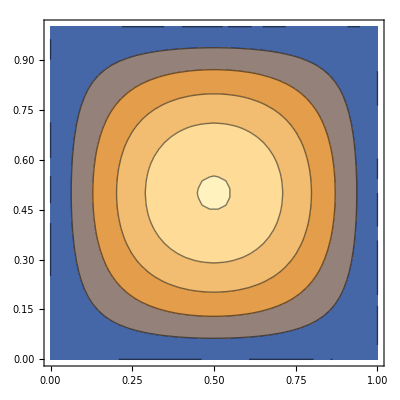

```mathematica
ContourPlot[sol[x,y],{x,0,1},{y,0,1}]
```

```mathematica
Plot3D[{sol[x,y]},{x,0,1},{y,0,1}]
Max[{realsol[x,y]}]
```

-Graphics3D-

```mathematica
0.05066059182116889 Sin[π x] Sin[π y]
N[Integrate[f1tri1[x,y]*func[x,y],{x,0,1},{y,0,1}]]
```

0.0506606 Sin[π x] Sin[π y]

0.0759909

```mathematica
results = {{0.5,0.5,-0.00900446},{0.25,0.5,0.00819999},{0.25,0.25,0.0110868},{0.5,0.75,0.00819999},{0.75,0.75,0.0113921},{0.25,0.75,0.0112256},{0.5,0.25,0.00726785},{0.75,0.5,0.00726785},{0.75,0.25,0.0107815},{0.75,0.5,-0.00507504},{0.75,0.25,0.0130871},{0,0,0},{0,0.25,0},{0,0.5,0},{1,1,0},{0.75,1,0},{0.5,1,0},{0,1,0},{0,0.75,0},{0.25,1,0},{0.25,0,0},{0.5,0,0},{1,0,0},{1,0.25,0},{1,0.5,0},{1,0.75,0}}
```

{{0.5,0.5,-0.00900446},{0.25,0.5,0.00819999},{0.25,0.25,0.0110868},{0.5,0.75,0.00819999},{0.75,0.75,0.0113921},{0.25,0.75,0.0112256},{0.5,0.25,0.00726785},{0.75,0.5,0.00726785},{0.75,0.25,0.0107815},{0.75,0.5,-0.00507504},{0.75,0.25,0.0130871},{0,0,0},{0,0.25,0},{0,0.5,0},{1,1,0},{0.75,1,0},{0.5,1,0},{0,1,0},{0,0.75,0},{0.25,1,0},{0.25,0,0},{0.5,0,0},{1,0,0},{1,0.25,0},{1,0.5,0},{1,0.75,0}}

```mathematica
{{0.5,0.5,-0.00900446},{0.25,0.5,0.00819999},{0.25,0.25,0.0110868},{0.5,0.75,0.00819999},{0.75,0.75,0.0113921},{0.25,0.75,0.0112256},{0.5,0.25,0.00726785},{0.75,0.5,0.00726785},{0.75,0.25,0.0107815},{0.75,0.5,-0.00507504},{0.75,0.25,0.0130871}}
ListPlot3D[results]
```

{{0.5,0.5,-0.00900446},{0.25,0.5,0.00819999},{0.25,0.25,0.0110868},{0.5,0.75,0.00819999},{0.75,0.75,0.0113921},{0.25,0.75,0.0112256},{0.5,0.25,0.00726785},{0.75,0.5,0.00726785},{0.75,0.25,0.0107815},{0.75,0.5,-0.00507504},{0.75,0.25,0.0130871}}

-Graphics3D-

```mathematica
ListPlot3D[{{0.5,0.5,-0.00900446},{0.25,0.5,0.00819999},{0.25,0.25,0.0110868},{0.5,0.75,0.00819999},{0.75,0.75,0.0113921},{0.25,0.75,0.0112256},{0.5,0.25,0.00726785},{0.75,0.5,0.00726785},{0.75,0.25,0.0107815},{0.75,0.5,-0.00507504},{0.75,0.25,0.0130871},{0,0,0},{0,0.25,0},{0,0.5,0},{1,1,0},{0.75,1,0},{0.5,1,0},{0,1,0},{0,0.75,0},{0.25,1,0},{0.25,0,0},{0.5,0,0},{1,0,0},{1,0.25,0},{1,0.5,0},{1,0.75,0}}]
results15nov = {{0.5,0.5,0.0726304},{0.25,0.25,0.0446327},{0.25,0.5,0.0566178},{0.75,0.75,0.0437651},{0.5,0.75,0.0563845},{0.25,0.75,0.0440398},{0.5,0.25,0.0564221},{0.75,0.25,0.0440038},{0.75,0.5,0.0563141},{0.125,0.125,0.0181221},{0.125,0.25,0.0277835},{0.375,0.375,0.0646877},{0.375,0.5,0.0684534},{0.25,0.375,0.0534304},{0.125,0.5,0.0343724},{0.125,0.375,0.0326661},{0.875,0.875,0.0177102},{0.75,0.875,0.0273994},{0.625,0.625,0.0646805},{0.5,0.625,0.0685945},{0.625,0.75,0.0532381},{0.5,0.875,0.0344718},{0.625,0.875,0.0326057},{0.125,0.875,0.0176795},{0.125,0.625,0.0327653},{0.125,0.75,0.0276624},{0.375,0.875,0.0326427},{0.25,0.875,0.0274904},{0.375,0.625,0.0648036},{0.25,0.625,0.0535297},{0.375,0.75,0.0533814},{0.25,0.125,0.0276116},{0.5,0.125,0.0343458},{0.375,0.125,0.0328382},{0.5,0.375,0.0683828},{0.375,0.25,0.0537804},{0.875,0.125,0.0177854},{0.625,0.125,0.0324944},{0.75,0.125,0.0274758},{0.875,0.375,0.0324952},{0.875,0.25,0.0273934},{0.875,0.75,0.0271528},{0.625,0.5,0.0687846},{0.75,0.625,0.05297},{0.875,0.5,0.0345986},{0.875,0.625,0.0325204},{0.625,0.25,0.0533219},{0.625,0.375,0.0646956},{0.75,0.375,0.0530809},{0,0,0},{0,0.125,0},{0,0.25,0},{0,0.5,0},{0,0.375,0},{1,1,0},{0.875,1,0},{0.75,1,0},{0.5,1,0},{0.625,1,0},{0,1,0},{0,0.875,0},{0.125,1,0},{0,0.75,0},{0.25,1,0},{0,0.625,0},{0.375,1,0},{0.125,0,0},{0.25,0,0},{0.5,0,0},{0.375,0,0},{1,0,0},{0.875,0,0},{1,0.125,0},{0.75,0,0},{1,0.25,0},{0.625,0,0},{1,0.5,0},{1,0.375,0},{1,0.875,0},{1,0.75,0},{1,0.625,0}}
```

-Graphics3D-

{{0.5,0.5,0.0726304},{0.25,0.25,0.0446327},{0.25,0.5,0.0566178},{0.75,0.75,0.0437651},{0.5,0.75,0.0563845},{0.25,0.75,0.0440398},{0.5,0.25,0.0564221},{0.75,0.25,0.0440038},{0.75,0.5,0.0563141},{0.125,0.125,0.0181221},{0.125,0.25,0.0277835},{0.375,0.375,0.0646877},{0.375,0.5,0.0684534},{0.25,0.375,0.0534304},{0.125,0.5,0.0343724},{0.125,0.375,0.0326661},{0.875,0.875,0.0177102},{0.75,0.875,0.0273994},{0.625,0.625,0.0646805},{0.5,0.625,0.0685945},{0.625,0.75,0.0532381},{0.5,0.875,0.0344718},{0.625,0.875,0.0326057},{0.125,0.875,0.0176795},{0.125,0.625,0.0327653},{0.125,0.75,0.0276624},{0.375,0.875,0.0326427},{0.25,0.875,0.0274904},{0.375,0.625,0.0648036},{0.25,0.625,0.0535297},{0.375,0.75,0.0533814},{0.25,0.125,0.0276116},{0.5,0.125,0.0343458},{0.375,0.125,0.0328382},{0.5,0.375,0.0683828},{0.375,0.25,0.0537804},{0.875,0.125,0.0177854},{0.625,0.125,0.0324944},{0.75,0.125,0.0274758},{0.875,0.375,0.0324952},{0.875,0.25,0.0273934},{0.875,0.75,0.0271528},{0.625,0.5,0.0687846},{0.75,0.625,0.05297},{0.875,0.5,0.0345986},{0.875,0.625,0.0325204},{0.625,0.25,0.0533219},{0.625,0.375,0.0646956},{0.75,0.375,0.0530809},{0,0,0},{0,0.125,0},{0,0.25,0},{0,0.5,0},{0,0.375,0},{1,1,0},{0.875,1,0},{0.75,1,0},{0.5,1,0},{0.625,1,0},{0,1,0},{0,0.875,0},{0.125,1,0},{0,0.75,0},{0.25,1,0},{0,0.625,0},{0.375,1,0},{0.125,0,0},{0.25,0,0},{0.5,0,0},{0.375,0,0},{1,0,0},{0.875,0,0},{1,0.125,0},{0.75,0,0},{1,0.25,0},{0.625,0,0},{1,0.5,0},{1,0.375,0},{1,0.875,0},{1,0.75,0},{1,0.625,0}}

```mathematica
ListPlot3D[results15nov]
```

-Graphics3D-

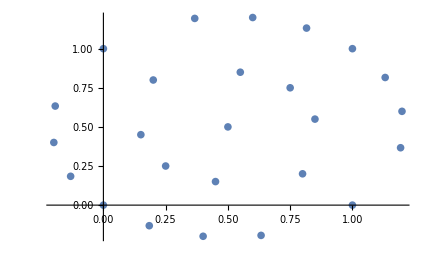

```mathematica
circlegrid := {{0.5,0.5},{0.25,0.25},{0.150452,0.450226},{0.75,0.75},{0.549774,0.849548},{0.200226,0.799774},{0.450226,0.150452},{0.799774,0.200226},{.849548,0.549774},{0,0},{-0.13158,0.18421},{-0.199097,0.400452},{1,1},{0.81579,1.13158},{0.599548,1.1991},{0,1},{-0.19345,0.633218},{0.366782,1.19345},{0.18421,-0.13158},{0.400452,-0.199097},{1,0},{.633218,-0.19345},{1.19345,0.366782},{1.1991,0.599548},{1.13158,0.81579}}
ListPlot[circlegrid]
```

```mathematica
refinedcirclegrid := {{0,0,-0.0791199},{0.799999,-0.6,0.275014},{-0.799999,-0.6,0.275014},{0.799999,0.6,0.275014},{-0.799999,0.6,0.275014},{0.5,0,-0.0676847},{0.399999,-0.3,-0.0820861},{-0.5,0,-0.0676847},{-0.399999,-0.3,-0.0820861},{0,-0.6,-0.0436085},{0.399999,0.3,-0.0820861},{0,0.6,-0.0436085},{-0.399999,0.3,-0.0820861},{0.75,0,0.0270288},{0.986749,-0.16225,-0.0397057},{0.724341,-0.158114,-0.0846495},{0.25,0,-0.0779777},{0.2,-0.15,-0.079284},{0.45,-0.15,-0.0765597},{0.886749,-0.46225,0.0283161},{0.599999,-0.45,-0.0505411},{0.674341,-0.308114,-0.103868},{-0.75,0,0.0270288},{-0.986749,-0.16225,-0.0397057},{-0.724341,-0.158114,-0.0846495},{-0.25,0,-0.0779777},{-0.2,-0.15,-0.079284},{-0.45,-0.15,-0.0765597},{-0.886749,-0.46225,0.0283161},{-0.599999,-0.45,-0.0505411},{-0.674341,-0.308114,-0.103868},{0,-0.827027,0.107485},{0.399999,-0.6,-0.153391},{0.28108,-0.713513,-0.117488},{-0.399999,-0.6,-0.153391},{-0.28108,-0.713513,-0.117488},{0,-0.3,-0.0785892},{0.2,-0.45,-0.0839072},{-0.2,-0.45,-0.0839072},{0.986749,0.16225,-0.0397057},{0.724341,0.158114,-0.0846495},{0.886749,0.46225,0.0283161},{0.599999,0.45,-0.0505411},{0.674341,0.308114,-0.103868},{0.2,0.15,-0.079284},{0.45,0.15,-0.0765597},{0,0.827027,0.107485},{0.399999,0.6,-0.153391},{0.28108,0.713513,-0.117488},{-0.399999,0.6,-0.153391},{-0.28108,0.713513,-0.117488},{-0.986749,0.16225,-0.0397057},{-0.724341,0.158114,-0.0846495},{-0.2,0.15,-0.079284},{-0.45,0.15,-0.0765597},{-0.886749,0.46225,0.0283161},{-0.599999,0.45,-0.0505411},{-0.674341,0.308114,-0.103868},{0.2,0.45,-0.0839072},{0,0.3,-0.0785892},{-0.2,0.45,-0.0839072},{0.875,0,0.265017},{0.868374,-0.0811248,0.141836},{0.625,0,-0.046154},{0.612171,-0.0790569,-0.058442},{0.737171,-0.0790569,-0.0161929},{0.836512,-0.237171,-0.280585},{0.855545,-0.160182,-0.0983219},{0.125,0,-0.0789485},{0.0999999,-0.075,-0.0791542},{0.225,-0.075,-0.0785255},{0.375,0,-0.0752474},{0.475,-0.075,-0.071987},{0.35,-0.075,-0.0766665},{0.3,-0.225,-0.0803044},{0.425,-0.225,-0.0796225},{0.325,-0.15,-0.0784896},{0.699999,-0.525,0.0552807},{0.743374,-0.456125,0.0710936},{0.811512,-0.312171,-0.278697},{0.780545,-0.385182,-0.113959},{0.499999,-0.375,-0.0793051},{0.53717,-0.304057,-0.0800296},{0.63717,-0.379057,-0.0622524},{0.58717,-0.154057,-0.0754545},{0.699341,-0.233114,-0.118471},{0.56217,-0.229057,-0.0825492},{-0.875,0,0.265017},{-0.868374,-0.0811248,0.141836},{-0.625,0,-0.046154},{-0.612171,-0.0790569,-0.058442},{-0.737171,-0.0790569,-0.0161929},{-0.836512,-0.237171,-0.280585},{-0.855545,-0.160182,-0.0983219},{-0.125,0,-0.0789485},{-0.0999999,-0.075,-0.0791542},{-0.225,-0.075,-0.0785255},{-0.375,0,-0.0752474},{-0.475,-0.075,-0.071987},{-0.35,-0.075,-0.0766665},{-0.3,-0.225,-0.0803044},{-0.425,-0.225,-0.0796225},{-0.325,-0.15,-0.0784896},{-0.699999,-0.525,0.0552807},{-0.743374,-0.456125,0.0710936},{-0.811512,-0.312171,-0.278697},{-0.780545,-0.385182,-0.113959},{-0.499999,-0.375,-0.0793051},{-0.53717,-0.304057,-0.0800296},{-0.63717,-0.379057,-0.0622524},{-0.58717,-0.154057,-0.0754545},{-0.699341,-0.233114,-0.118471},{-0.56217,-0.229057,-0.0825492},{0.25728,-0.966336,-0.271554},{-0.25728,-0.966336,-0.271554},{0,-0.923923,-0.313068},{0.481551,-0.876417,-0.123408},{0.28108,-0.827027,0.0480357},{0.191288,-0.875475,0.120923},{-0.481551,-0.876417,-0.123408},{-0.28108,-0.827027,0.0480357},{-0.191288,-0.875475,0.120923},{0.752378,-0.65873,0.0577439},{0.599999,-0.6,-0.115907},{0.548896,-0.658149,-0.219346},{0.635011,-0.772502,-0.496078},{0.421621,-0.77027,-0.351717},{0.489436,-0.714906,-0.32754},{0.2,-0.6,-0.0736577},{0.14054,-0.656756,-0.033149},{0.34054,-0.656756,-0.157996},{-0.752378,-0.65873,0.0577439},{-0.599999,-0.6,-0.115907},{-0.548896,-0.658149,-0.219346},{-0.635011,-0.772502,-0.496078},{-0.421621,-0.77027,-0.351717},{-0.489436,-0.714906,-0.32754},{-0.2,-0.6,-0.0736577},{-0.14054,-0.656756,-0.033149},{-0.34054,-0.656756,-0.157996},{0.14054,-0.77027,0.0662322},{-0.14054,-0.77027,0.0662322},{0,-0.713513,0.0520038},{0,-0.15,-0.0794572},{0.2,-0.3,-0.0816867},{0.0999999,-0.225,-0.0797225},{-0.2,-0.3,-0.0816867},{-0.0999999,-0.225,-0.0797225},{0.499999,-0.525,-0.114907},{0.3,-0.375,-0.0879961},{0.399999,-0.45,-0.100246},{0.0999999,-0.525,-0.0658142},{0.3,-0.525,-0.104328},{-0.499999,-0.525,-0.114907},{-0.3,-0.375,-0.0879961},{-0.399999,-0.45,-0.100246},{-0.0999999,-0.525,-0.0658142},{-0.3,-0.525,-0.104328},{0.0999999,-0.375,-0.0781335},{-0.0999999,-0.375,-0.0781335},{0,-0.45,-0.0705084},{0.868374,0.0811248,0.141836},{0.836512,0.237171,-0.280585},{0.855545,0.160182,-0.0983219},{0.612171,0.0790569,-0.058442},{0.737171,0.0790569,-0.0161929},{0.699999,0.525,0.0552807},{0.743374,0.456125,0.0710936},{0.811512,0.312171,-0.278697},{0.780545,0.385182,-0.113959},{0.499999,0.375,-0.0793051},{0.53717,0.304057,-0.0800296},{0.63717,0.379057,-0.0622524},{0.0999999,0.075,-0.0791542},{0.225,0.075,-0.0785255},{0.475,0.075,-0.071987},{0.35,0.075,-0.0766665},{0.3,0.225,-0.0803044},{0.425,0.225,-0.0796225},{0.325,0.15,-0.0784896},{0.699341,0.233114,-0.118471},{0.58717,0.154057,-0.0754545},{0.56217,0.229057,-0.0825492},{0.25728,0.966336,-0.271554},{-0.25728,0.966336,-0.271554},{0,0.923923,-0.313068},{0.481551,0.876417,-0.123408},{0.28108,0.827027,0.0480357},{0.191288,0.875475,0.120923},{-0.481551,0.876417,-0.123408},{-0.28108,0.827027,0.0480357},{-0.191288,0.875475,0.120923},{0.752378,0.65873,0.0577439},{0.599999,0.6,-0.115907},{0.548896,0.658149,-0.219346},{0.635011,0.772502,-0.496078},{0.421621,0.77027,-0.351717},{0.489436,0.714906,-0.32754},{0.2,0.6,-0.0736577},{0.14054,0.656756,-0.033149},{0.34054,0.656756,-0.157996},{-0.752378,0.65873,0.0577439},{-0.599999,0.6,-0.115907},{-0.548896,0.658149,-0.219346},{-0.635011,0.772502,-0.496078},{-0.421621,0.77027,-0.351717},{-0.489436,0.714906,-0.32754},{-0.2,0.6,-0.0736577},{-0.14054,0.656756,-0.033149},{-0.34054,0.656756,-0.157996},{0.14054,0.77027,0.0662322},{-0.14054,0.77027,0.0662322},{0,0.713513,0.0520038},{-0.868374,0.0811248,0.141836},{-0.612171,0.0790569,-0.058442},{-0.737171,0.0790569,-0.0161929},{-0.836512,0.237171,-0.280585},{-0.855545,0.160182,-0.0983219},{-0.0999999,0.075,-0.0791542},{-0.225,0.075,-0.0785255},{-0.475,0.075,-0.071987},{-0.35,0.075,-0.0766665},{-0.3,0.225,-0.0803044},{-0.425,0.225,-0.0796225},{-0.325,0.15,-0.0784896},{-0.699999,0.525,0.0552807},{-0.743374,0.456125,0.0710936},{-0.811512,0.312171,-0.278697},{-0.780545,0.385182,-0.113959},{-0.499999,0.375,-0.0793051},{-0.53717,0.304057,-0.0800296},{-0.63717,0.379057,-0.0622524},{-0.58717,0.154057,-0.0754545},{-0.699341,0.233114,-0.118471},{-0.56217,0.229057,-0.0825492},{0.499999,0.525,-0.114907},{0.3,0.375,-0.0879961},{0.399999,0.45,-0.100246},{0.0999999,0.525,-0.0658142},{0.3,0.525,-0.104328},{0,0.15,-0.0794572},{0.2,0.3,-0.0816867},{0.0999999,0.225,-0.0797225},{-0.2,0.3,-0.0816867},{-0.0999999,0.225,-0.0797225},{-0.499999,0.525,-0.114907},{-0.0999999,0.525,-0.0658142},{-0.3,0.525,-0.104328},{-0.3,0.375,-0.0879961},{-0.399999,0.45,-0.100246},{0.0999999,0.375,-0.0781335},{0,0.45,-0.0705084},{-0.0999999,0.375,-0.0781335},{1,0,1},{0.996614,-0.0822048,0.680041},{0.948682,-0.316227,-0.99712},{0.970713,-0.240238,-0.754776},{0.846614,-0.532205,0.783106},{0.920713,-0.390238,-0.646881},{-1,0,1},{-0.996614,-0.0822048,0.680041},{-0.948682,-0.316227,-0.99712},{-0.970713,-0.240238,-0.754776},{-0.846614,-0.532205,0.783106},{-0.920713,-0.390238,-0.646881},{0,-1,-1},{0.382575,-0.923923,0.70793},{-0.382575,-0.923923,0.70793},{0.562161,-0.827027,-0.951347},{-0.562161,-0.827027,-0.951347},{0.697792,-0.716299,-0.130489},{-0.697792,-0.716299,-0.130489},{0.996614,0.0822048,0.680041},{0.948682,0.316227,-0.99712},{0.970713,0.240238,-0.754776},{0.846614,0.532205,0.783106},{0.920713,0.390238,-0.646881},{0,1,-1},{0.382575,0.923923,0.70793},{-0.382575,0.923923,0.70793},{0.562161,0.827027,-0.951347},{-0.562161,0.827027,-0.951347},{0.697792,0.716299,-0.130489},{-0.697792,0.716299,-0.130489},{-0.996614,0.0822048,0.680041},{-0.948682,0.316227,-0.99712},{-0.970713,0.240238,-0.754776},{-0.846614,0.532205,0.783106},{-0.920713,0.390238,-0.646881}}
```

```mathematica
ListPlot3D[refinedcirclegrid]
```

-Graphics3D-

```mathematica
refinedcsol := {{0,0,-0.13174},{0.799999,-0.6,0.691208},{-0.799999,-0.6,0.691208},{0.799999,0.6,0.691208},{-0.799999,0.6,0.691208},{0.5,0,-0.0888596},{0.399999,-0.3,-0.115003},{-0.5,0,-0.0888596},{-0.399999,-0.3,-0.115003},{0,-0.6,-0.196653},{0.399999,0.3,-0.115003},{0,0.6,-0.196653},{-0.399999,0.3,-0.115003},{0.75,0,0.00721887},{0.986749,-0.16225,-0.037155},{0.724341,-0.158114,-0.0782073},{0.25,0,-0.121014},{0.2,-0.15,-0.128921},{0.45,-0.15,-0.100597},{0.886749,-0.46225,0.0153509},{0.599999,-0.45,-0.0291804},{0.674341,-0.308114,-0.08604},{-0.75,0,0.00721887},{-0.986749,-0.16225,-0.037155},{-0.724341,-0.158114,-0.0782073},{-0.25,0,-0.121014},{-0.2,-0.15,-0.128921},{-0.45,-0.15,-0.100597},{-0.886749,-0.46225,0.0153509},{-0.599999,-0.45,-0.0291804},{-0.674341,-0.308114,-0.08604},{0,-0.827027,-0.32486},{0.399999,-0.6,-0.199108},{0.28108,-0.713513,-0.202859},{-0.399999,-0.6,-0.199108},{-0.28108,-0.713513,-0.202859},{0,-0.3,-0.149016},{0.2,-0.45,-0.163871},{-0.2,-0.45,-0.163871},{0.986749,0.16225,-0.037155},{0.724341,0.158114,-0.0782073},{0.886749,0.46225,0.0153509},{0.599999,0.45,-0.0291804},{0.674341,0.308114,-0.08604},{0.2,0.15,-0.128921},{0.45,0.15,-0.100597},{0,0.827027,-0.32486},{0.399999,0.6,-0.199108},{0.28108,0.713513,-0.202859},{-0.399999,0.6,-0.199108},{-0.28108,0.713513,-0.202859},{-0.986749,0.16225,-0.037155},{-0.724341,0.158114,-0.0782073},{-0.2,0.15,-0.128921},{-0.45,0.15,-0.100597},{-0.886749,0.46225,0.0153509},{-0.599999,0.45,-0.0291804},{-0.674341,0.308114,-0.08604},{0.2,0.45,-0.163871},{0,0.3,-0.149016},{-0.2,0.45,-0.163871},{0.875,0,0.218619},{0.868374,-0.0811248,0.11571},{0.625,0,-0.0601625},{0.612171,-0.0790569,-0.0695983},{0.737171,-0.0790569,-0.026054},{0.836512,-0.237171,-0.239867},{0.855545,-0.160182,-0.0875124},{0.125,0,-0.129304},{0.0999999,-0.075,-0.131344},{0.225,-0.075,-0.124062},{0.375,0,-0.107527},{0.475,-0.075,-0.0943548},{0.35,-0.075,-0.111466},{0.3,-0.225,-0.124155},{0.425,-0.225,-0.106984},{0.325,-0.15,-0.116906},{0.699999,-0.525,0.170295},{0.743374,-0.456125,0.102139},{0.811512,-0.312171,-0.233734},{0.780545,-0.385182,-0.0811642},{0.499999,-0.375,-0.0933799},{0.53717,-0.304057,-0.0882532},{0.63717,-0.379057,-0.0464889},{0.58717,-0.154057,-0.0831035},{0.699341,-0.233114,-0.103205},{0.56217,-0.229057,-0.089105},{-0.875,0,0.218619},{-0.868374,-0.0811248,0.11571},{-0.625,0,-0.0601625},{-0.612171,-0.0790569,-0.0695983},{-0.737171,-0.0790569,-0.026054},{-0.836512,-0.237171,-0.239867},{-0.855545,-0.160182,-0.0875124},{-0.125,0,-0.129304},{-0.0999999,-0.075,-0.131344},{-0.225,-0.075,-0.124062},{-0.375,0,-0.107527},{-0.475,-0.075,-0.0943548},{-0.35,-0.075,-0.111466},{-0.3,-0.225,-0.124155},{-0.425,-0.225,-0.106984},{-0.325,-0.15,-0.116906},{-0.699999,-0.525,0.170295},{-0.743374,-0.456125,0.102139},{-0.811512,-0.312171,-0.233734},{-0.780545,-0.385182,-0.0811642},{-0.499999,-0.375,-0.0933799},{-0.53717,-0.304057,-0.0882532},{-0.63717,-0.379057,-0.0464889},{-0.58717,-0.154057,-0.0831035},{-0.699341,-0.233114,-0.103205},{-0.56217,-0.229057,-0.089105},{0.25728,-0.966336,-0.35104},{-0.25728,-0.966336,-0.35104},{0,-0.923923,-0.580968},{0.481551,-0.876417,-0.250151},{0.28108,-0.827027,-0.0941039},{0.191288,-0.875475,-0.20577},{-0.481551,-0.876417,-0.250151},{-0.28108,-0.827027,-0.0941039},{-0.191288,-0.875475,-0.20577},{0.752378,-0.65873,0.515251},{0.599999,-0.6,-0.0698692},{0.548896,-0.658149,-0.25093},{0.635011,-0.772502,-0.699166},{0.421621,-0.77027,-0.296673},{0.489436,-0.714906,-0.358164},{0.2,-0.6,-0.192835},{0.14054,-0.656756,-0.20488},{0.34054,-0.656756,-0.215251},{-0.752378,-0.65873,0.515251},{-0.599999,-0.6,-0.0698692},{-0.548896,-0.658149,-0.25093},{-0.635011,-0.772502,-0.699166},{-0.421621,-0.77027,-0.296673},{-0.489436,-0.714906,-0.358164},{-0.2,-0.6,-0.192835},{-0.14054,-0.656756,-0.20488},{-0.34054,-0.656756,-0.215251},{0.14054,-0.77027,-0.223969},{-0.14054,-0.77027,-0.223969},{0,-0.713513,-0.231281},{0,-0.15,-0.136348},{0.2,-0.3,-0.141366},{0.0999999,-0.225,-0.13975},{-0.2,-0.3,-0.141366},{-0.0999999,-0.225,-0.13975},{0.499999,-0.525,-0.121937},{0.3,-0.375,-0.140857},{0.399999,-0.45,-0.136634},{0.0999999,-0.525,-0.181257},{0.3,-0.525,-0.173768},{-0.499999,-0.525,-0.121937},{-0.3,-0.375,-0.140857},{-0.399999,-0.45,-0.136634},{-0.0999999,-0.525,-0.181257},{-0.3,-0.525,-0.173768},{0.0999999,-0.375,-0.15672},{-0.0999999,-0.375,-0.15672},{0,-0.45,-0.169616},{0.868374,0.0811248,0.11571},{0.836512,0.237171,-0.239867},{0.855545,0.160182,-0.0875124},{0.612171,0.0790569,-0.0695983},{0.737171,0.0790569,-0.026054},{0.699999,0.525,0.170295},{0.743374,0.456125,0.102139},{0.811512,0.312171,-0.233734},{0.780545,0.385182,-0.0811642},{0.499999,0.375,-0.0933799},{0.53717,0.304057,-0.0882532},{0.63717,0.379057,-0.0464889},{0.0999999,0.075,-0.131344},{0.225,0.075,-0.124062},{0.475,0.075,-0.0943548},{0.35,0.075,-0.111466},{0.3,0.225,-0.124155},{0.425,0.225,-0.106984},{0.325,0.15,-0.116906},{0.699341,0.233114,-0.103205},{0.58717,0.154057,-0.0831035},{0.56217,0.229057,-0.089105},{0.25728,0.966336,-0.35104},{-0.25728,0.966336,-0.35104},{0,0.923923,-0.580968},{0.481551,0.876417,-0.250151},{0.28108,0.827027,-0.0941039},{0.191288,0.875475,-0.20577},{-0.481551,0.876417,-0.250151},{-0.28108,0.827027,-0.0941039},{-0.191288,0.875475,-0.20577},{0.752378,0.65873,0.515251},{0.599999,0.6,-0.0698692},{0.548896,0.658149,-0.25093},{0.635011,0.772502,-0.699166},{0.421621,0.77027,-0.296673},{0.489436,0.714906,-0.358164},{0.2,0.6,-0.192835},{0.14054,0.656756,-0.20488},{0.34054,0.656756,-0.215251},{-0.752378,0.65873,0.515251},{-0.599999,0.6,-0.0698692},{-0.548896,0.658149,-0.25093},{-0.635011,0.772502,-0.699166},{-0.421621,0.77027,-0.296673},{-0.489436,0.714906,-0.358164},{-0.2,0.6,-0.192835},{-0.14054,0.656756,-0.20488},{-0.34054,0.656756,-0.215251},{0.14054,0.77027,-0.223969},{-0.14054,0.77027,-0.223969},{0,0.713513,-0.231281},{-0.868374,0.0811248,0.11571},{-0.612171,0.0790569,-0.0695983},{-0.737171,0.0790569,-0.026054},{-0.836512,0.237171,-0.239867},{-0.855545,0.160182,-0.0875124},{-0.0999999,0.075,-0.131344},{-0.225,0.075,-0.124062},{-0.475,0.075,-0.0943548},{-0.35,0.075,-0.111466},{-0.3,0.225,-0.124155},{-0.425,0.225,-0.106984},{-0.325,0.15,-0.116906},{-0.699999,0.525,0.170295},{-0.743374,0.456125,0.102139},{-0.811512,0.312171,-0.233734},{-0.780545,0.385182,-0.0811642},{-0.499999,0.375,-0.0933799},{-0.53717,0.304057,-0.0882532},{-0.63717,0.379057,-0.0464889},{-0.58717,0.154057,-0.0831035},{-0.699341,0.233114,-0.103205},{-0.56217,0.229057,-0.089105},{0.499999,0.525,-0.121937},{0.3,0.375,-0.140857},{0.399999,0.45,-0.136634},{0.0999999,0.525,-0.181257},{0.3,0.525,-0.173768},{0,0.15,-0.136348},{0.2,0.3,-0.141366},{0.0999999,0.225,-0.13975},{-0.2,0.3,-0.141366},{-0.0999999,0.225,-0.13975},{-0.499999,0.525,-0.121937},{-0.0999999,0.525,-0.181257},{-0.3,0.525,-0.173768},{-0.3,0.375,-0.140857},{-0.399999,0.45,-0.136634},{0.0999999,0.375,-0.15672},{0,0.45,-0.169616},{-0.0999999,0.375,-0.15672},{0.9375,0,0.470779},{0.999142,-0.0413808,0.711447},{0.935807,-0.0411024,0.404514},{0.8125,0,0.0820108},{0.809187,-0.0405624,0.0641222},{0.871687,-0.0405624,0.185272},{0.992469,-0.12249,0.269355},{0.927562,-0.121687,0.110482},{0.932494,-0.0816648,0.293473},{0.5625,0,-0.0766245},{0.556085,-0.0395284,-0.0788212},{0.618585,-0.0395284,-0.0637595},{0.6875,0,-0.0351281},{0.743585,-0.0395284,-0.0047678},{0.681085,-0.0395284,-0.0415706},{0.668256,-0.118585,-0.0658955},{0.730756,-0.118585,-0.0521988},{0.674671,-0.0790569,-0.0526757},{0.960441,-0.27848,-0.754529},{0.892597,-0.276699,-0.4719},{0.903612,-0.238704,-0.404612},{0.979488,-0.201496,-0.343691},{0.921147,-0.161216,-0.0817557},{0.913129,-0.20021,-0.265966},{0.780426,-0.197642,-0.125066},{0.789943,-0.159148,-0.0823636},{0.846028,-0.198676,-0.177733},{0.802772,-0.0800908,0.0228364},{0.86196,-0.120653,0.0170107},{0.796358,-0.119619,-0.0289268},{0.0625,0,-0.131318},{0.0499999,-0.0375,-0.131825},{0.1125,-0.0375,-0.130087},{0.1875,0,-0.125846},{0.2375,-0.0375,-0.122322},{0.175,-0.0375,-0.126898},{0.15,-0.1125,-0.13038},{0.2125,-0.1125,-0.126254},{0.1625,-0.075,-0.128405},{0.4375,0,-0.0989377},{0.4875,-0.0375,-0.0914061},{0.425,-0.0375,-0.101007},{0.3125,0,-0.114885},{0.3,-0.0375,-0.116432},{0.3625,-0.0375,-0.109311},{0.4625,-0.1125,-0.0974674},{0.4,-0.1125,-0.106143},{0.4125,-0.075,-0.103433},{0.35,-0.2625,-0.120397},{0.4125,-0.2625,-0.110625},{0.3625,-0.225,-0.1161},{0.25,-0.1875,-0.126895},{0.2625,-0.15,-0.123579},{0.3125,-0.1875,-0.120268},{0.4375,-0.1875,-0.103727},{0.3875,-0.15,-0.109114},{0.375,-0.1875,-0.112395},{0.2875,-0.075,-0.118382},{0.275,-0.1125,-0.120755},{0.3375,-0.1125,-0.11399},{0.824142,-0.566381,0.625002},{0.749999,-0.5625,0.379597},{0.773307,-0.528602,0.358354},{0.867469,-0.49749,0.329421},{0.815061,-0.459187,0.129573},{0.794994,-0.494165,0.296365},{0.649999,-0.4875,0.043539},{0.671687,-0.453062,0.0354373},{0.721687,-0.490562,0.153053},{0.935441,-0.35348,-0.71059},{0.880097,-0.314199,-0.461552},{0.866112,-0.351204,-0.37596},{0.904488,-0.426496,-0.277279},{0.833647,-0.423716,-0.0541677},{0.850629,-0.38771,-0.232863},{0.742926,-0.310142,-0.12615},{0.727443,-0.346648,-0.0865443},{0.796028,-0.348676,-0.169112},{0.449999,-0.3375,-0.106795},{0.468585,-0.302028,-0.101716},{0.518585,-0.339528,-0.0894579},{0.549999,-0.4125,-0.0702459},{0.618585,-0.414528,-0.0330186},{0.568585,-0.377028,-0.0690157},{0.605756,-0.306085,-0.0795419},{0.655756,-0.343585,-0.0657241},{0.58717,-0.341557,-0.0729125},{0.761959,-0.420653,0.0157402},{0.690272,-0.417591,0.00425531},{0.708857,-0.382119,-0.039128},{0.543585,-0.0770284,-0.0831038},{0.655756,-0.156085,-0.0780515},{0.599671,-0.116557,-0.0769946},{0.518585,-0.152028,-0.0912308},{0.531085,-0.114528,-0.0873987},{0.824012,-0.274671,-0.256726},{0.711841,-0.195614,-0.0958959},{0.767926,-0.235142,-0.146804},{0.686841,-0.270614,-0.0995334},{0.755426,-0.272642,-0.146958},{0.481085,-0.264528,-0.0991519},{0.506085,-0.189528,-0.0943769},{0.493585,-0.227028,-0.0969014},{0.618256,-0.268585,-0.0859687},{0.54967,-0.266557,-0.0891664},{0.643256,-0.193585,-0.0858316},{0.57467,-0.191557,-0.0872033},{0.630756,-0.231085,-0.0884225},{-0.9375,0,0.470779},{-0.999142,-0.0413808,0.711447},{-0.935807,-0.0411024,0.404514},{-0.8125,0,0.0820108},{-0.809187,-0.0405624,0.0641222},{-0.871687,-0.0405624,0.185272},{-0.992469,-0.12249,0.269355},{-0.927562,-0.121687,0.110482},{-0.932494,-0.0816648,0.293473},{-0.5625,0,-0.0766245},{-0.556085,-0.0395284,-0.0788212},{-0.618585,-0.0395284,-0.0637595},{-0.6875,0,-0.0351281},{-0.743585,-0.0395284,-0.0047678},{-0.681085,-0.0395284,-0.0415706},{-0.668256,-0.118585,-0.0658955},{-0.730756,-0.118585,-0.0521988},{-0.674671,-0.0790569,-0.0526757},{-0.960441,-0.27848,-0.754529},{-0.892597,-0.276699,-0.4719},{-0.903612,-0.238704,-0.404612},{-0.979488,-0.201496,-0.343691},{-0.921147,-0.161216,-0.0817557},{-0.913129,-0.20021,-0.265966},{-0.780426,-0.197642,-0.125066},{-0.789943,-0.159148,-0.0823636},{-0.846028,-0.198676,-0.177733},{-0.802772,-0.0800908,0.0228364},{-0.86196,-0.120653,0.0170107},{-0.796358,-0.119619,-0.0289268},{-0.0625,0,-0.131318},{-0.0499999,-0.0375,-0.131825},{-0.1125,-0.0375,-0.130087},{-0.1875,0,-0.125846},{-0.2375,-0.0375,-0.122322},{-0.175,-0.0375,-0.126898},{-0.15,-0.1125,-0.13038},{-0.2125,-0.1125,-0.126254},{-0.1625,-0.075,-0.128405},{-0.4375,0,-0.0989377},{-0.4875,-0.0375,-0.0914061},{-0.425,-0.0375,-0.101007},{-0.3125,0,-0.114885},{-0.3,-0.0375,-0.116432},{-0.3625,-0.0375,-0.109311},{-0.4625,-0.1125,-0.0974674},{-0.4,-0.1125,-0.106143},{-0.4125,-0.075,-0.103433},{-0.35,-0.2625,-0.120397},{-0.4125,-0.2625,-0.110625},{-0.3625,-0.225,-0.1161},{-0.25,-0.1875,-0.126895},{-0.2625,-0.15,-0.123579},{-0.3125,-0.1875,-0.120268},{-0.4375,-0.1875,-0.103727},{-0.3875,-0.15,-0.109114},{-0.375,-0.1875,-0.112395},{-0.2875,-0.075,-0.118382},{-0.275,-0.1125,-0.120755},{-0.3375,-0.1125,-0.11399},{-0.824142,-0.566381,0.625002},{-0.749999,-0.5625,0.379597},{-0.773307,-0.528602,0.358354},{-0.867469,-0.49749,0.329421},{-0.815061,-0.459187,0.129573},{-0.794994,-0.494165,0.296365},{-0.649999,-0.4875,0.043539},{-0.671687,-0.453062,0.0354373},{-0.721687,-0.490562,0.153053},{-0.935441,-0.35348,-0.71059},{-0.880097,-0.314199,-0.461552},{-0.866112,-0.351204,-0.37596},{-0.904488,-0.426496,-0.277279},{-0.833647,-0.423716,-0.0541677},{-0.850629,-0.38771,-0.232863},{-0.742926,-0.310142,-0.12615},{-0.727443,-0.346648,-0.0865443},{-0.796028,-0.348676,-0.169112},{-0.449999,-0.3375,-0.106795},{-0.468585,-0.302028,-0.101716},{-0.518585,-0.339528,-0.0894579},{-0.549999,-0.4125,-0.0702459},{-0.618585,-0.414528,-0.0330186},{-0.568585,-0.377028,-0.0690157},{-0.605756,-0.306085,-0.0795419},{-0.655756,-0.343585,-0.0657241},{-0.58717,-0.341557,-0.0729125},{-0.761959,-0.420653,0.0157402},{-0.690272,-0.417591,0.00425531},{-0.708857,-0.382119,-0.039128},{-0.543585,-0.0770284,-0.0831038},{-0.655756,-0.156085,-0.0780515},{-0.599671,-0.116557,-0.0769946},{-0.518585,-0.152028,-0.0912308},{-0.531085,-0.114528,-0.0873987},{-0.824012,-0.274671,-0.256726},{-0.711841,-0.195614,-0.0958959},{-0.767926,-0.235142,-0.146804},{-0.686841,-0.270614,-0.0995334},{-0.755426,-0.272642,-0.146958},{-0.481085,-0.264528,-0.0991519},{-0.506085,-0.189528,-0.0943769},{-0.493585,-0.227028,-0.0969014},{-0.618256,-0.268585,-0.0859687},{-0.54967,-0.266557,-0.0891664},{-0.643256,-0.193585,-0.0858316},{-0.57467,-0.191557,-0.0872033},{-0.630756,-0.231085,-0.0884225},{0.172169,-0.985066,-0.728585},{-0.172169,-0.985066,-0.728585},{0,-0.966336,-0.753426},{0.325603,-0.945506,0.182014},{0.191288,-0.923923,-0.356985},{0.12864,-0.94513,-0.585249},{-0.325603,-0.945506,0.182014},{-0.191288,-0.923923,-0.356985},{-0.12864,-0.94513,-0.585249},{0.421621,-0.827027,-0.204029},{0.381316,-0.851722,-0.0114808},{0.286932,-0.899699,0.111685},{0.336419,-0.875946,0.116444},{0.14054,-0.827027,-0.259759},{0.0956439,-0.851251,-0.339366},{0.236184,-0.851251,-0.114403},{-0.421621,-0.827027,-0.204029},{-0.381316,-0.851722,-0.0114808},{-0.286932,-0.899699,0.111685},{-0.336419,-0.875946,0.116444},{-0.14054,-0.827027,-0.259759},{-0.0956439,-0.851251,-0.339366},{-0.236184,-0.851251,-0.114403},{0.0956439,-0.899699,-0.470466},{-0.0956439,-0.899699,-0.470466},{0,-0.875475,-0.465739},{0.699999,-0.6,0.254374},{0.676189,-0.629365,0.106467},{0.623344,-0.687224,-0.251321},{0.650637,-0.658439,-0.0584483},{0.499999,-0.6,-0.181059},{0.474448,-0.629074,-0.222508},{0.574448,-0.629074,-0.161183},{0.491891,-0.798648,-0.500994},{0.528316,-0.771386,-0.578018},{0.593614,-0.715602,-0.418861},{0.562224,-0.743704,-0.521089},{0.35135,-0.741892,-0.221452},{0.385258,-0.71421,-0.251129},{0.455529,-0.742588,-0.35204},{0.0999999,-0.6,-0.195534},{0.0702701,-0.628378,-0.202146},{0.17027,-0.628378,-0.198429},{0.3,-0.6,-0.194338},{0.37027,-0.628378,-0.211712},{0.27027,-0.628378,-0.198774},{0.21081,-0.685135,-0.203416},{0.31081,-0.685135,-0.211254},{0.24054,-0.656756,-0.201052},{0.519166,-0.686528,-0.321545},{0.444718,-0.657453,-0.25084},{0.414988,-0.685831,-0.260338},{-0.699999,-0.6,0.254374},{-0.676189,-0.629365,0.106467},{-0.623344,-0.687224,-0.251321},{-0.650637,-0.658439,-0.0584483},{-0.499999,-0.6,-0.181059},{-0.474448,-0.629074,-0.222508},{-0.574448,-0.629074,-0.161183},{-0.491891,-0.798648,-0.500994},{-0.528316,-0.771386,-0.578018},{-0.593614,-0.715602,-0.418861},{-0.562224,-0.743704,-0.521089},{-0.35135,-0.741892,-0.221452},{-0.385258,-0.71421,-0.251129},{-0.455529,-0.742588,-0.35204},{-0.0999999,-0.6,-0.195534},{-0.0702701,-0.628378,-0.202146},{-0.17027,-0.628378,-0.198429},{-0.3,-0.6,-0.194338},{-0.37027,-0.628378,-0.211712},{-0.27027,-0.628378,-0.198774},{-0.21081,-0.685135,-0.203416},{-0.31081,-0.685135,-0.211254},{-0.24054,-0.656756,-0.201052},{-0.519166,-0.686528,-0.321545},{-0.444718,-0.657453,-0.25084},{-0.414988,-0.685831,-0.260338},{0.35135,-0.798648,-0.150782},{0.0702701,-0.798648,-0.279931},{0.21081,-0.798648,-0.178301},{0.21081,-0.741892,-0.193621},{0.28108,-0.77027,-0.166385},{-0.35135,-0.798648,-0.150782},{-0.0702701,-0.798648,-0.279931},{-0.21081,-0.798648,-0.178301},{-0.21081,-0.741892,-0.193621},{-0.28108,-0.77027,-0.166385},{0,-0.656756,-0.210043},{0.14054,-0.713513,-0.21174},{0.0702701,-0.685135,-0.21578},{-0.14054,-0.713513,-0.21174},{-0.0702701,-0.685135,-0.21578},{0,-0.77027,-0.268608},{0.0702701,-0.741892,-0.238605},{-0.0702701,-0.741892,-0.238605},{0,-0.075,-0.13312},{0.0999999,-0.15,-0.134495},{0.0499999,-0.1125,-0.134026},{-0.0999999,-0.15,-0.134495},{-0.0499999,-0.1125,-0.134026},{0.3,-0.3,-0.130882},{0.25,-0.2625,-0.132841},{0.15,-0.1875,-0.134495},{0.2,-0.225,-0.133977},{0.0999999,-0.3,-0.147166},{0.0499999,-0.2625,-0.144601},{0.15,-0.2625,-0.140791},{-0.3,-0.3,-0.130882},{-0.25,-0.2625,-0.132841},{-0.15,-0.1875,-0.134495},{-0.2,-0.225,-0.133977},{-0.0999999,-0.3,-0.147166},{-0.0499999,-0.2625,-0.144601},{-0.15,-0.2625,-0.140791},{0.0499999,-0.1875,-0.138264},{-0.0499999,-0.1875,-0.138264},{0,-0.225,-0.141639},{0.649999,-0.5625,0.0777276},{0.549999,-0.4875,-0.0694125},{0.599999,-0.525,-0.0176127},{0.449999,-0.5625,-0.168714},{0.549999,-0.5625,-0.104021},{0.35,-0.3375,-0.127685},{0.399999,-0.375,-0.122435},{0.499999,-0.45,-0.0977889},{0.449999,-0.4125,-0.113508},{0.25,-0.4125,-0.153155},{0.3,-0.45,-0.155108},{0.35,-0.4125,-0.139425},{0.0499999,-0.5625,-0.189082},{0.15,-0.5625,-0.18699},{0.35,-0.5625,-0.182902},{0.25,-0.5625,-0.184797},{0.15,-0.4875,-0.173054},{0.25,-0.4875,-0.16806},{0.2,-0.525,-0.178313},{0.449999,-0.4875,-0.131478},{0.399999,-0.525,-0.161706},{0.35,-0.4875,-0.157668},{-0.649999,-0.5625,0.0777276},{-0.549999,-0.4875,-0.0694125},{-0.599999,-0.525,-0.0176127},{-0.449999,-0.5625,-0.168714},{-0.549999,-0.5625,-0.104021},{-0.35,-0.3375,-0.127685},{-0.399999,-0.375,-0.122435},{-0.499999,-0.45,-0.0977889},{-0.449999,-0.4125,-0.113508},{-0.25,-0.4125,-0.153155},{-0.3,-0.45,-0.155108},{-0.35,-0.4125,-0.139425},{-0.0499999,-0.5625,-0.189082},{-0.15,-0.5625,-0.18699},{-0.35,-0.5625,-0.182902},{-0.25,-0.5625,-0.184797},{-0.15,-0.4875,-0.173054},{-0.25,-0.4875,-0.16806},{-0.2,-0.525,-0.178313},{-0.449999,-0.4875,-0.131478},{-0.399999,-0.525,-0.161706},{-0.35,-0.4875,-0.157668},{0.25,-0.3375,-0.141426},{0.0499999,-0.3375,-0.153026},{0.15,-0.3375,-0.149382},{0.15,-0.4125,-0.160251},{0.2,-0.375,-0.151331},{-0.25,-0.3375,-0.141426},{-0.0499999,-0.3375,-0.153026},{-0.15,-0.3375,-0.149382},{-0.15,-0.4125,-0.160251},{-0.2,-0.375,-0.151331},{0,-0.525,-0.182426},{0.0999999,-0.45,-0.168219},{0.0499999,-0.4875,-0.175514},{-0.0999999,-0.45,-0.168219},{-0.0499999,-0.4875,-0.175514},{0,-0.375,-0.158403},{0.0499999,-0.4125,-0.163413},{-0.0499999,-0.4125,-0.163413},{0.999142,0.0413808,0.711447},{0.935807,0.0411024,0.404514},{0.992469,0.12249,0.269355},{0.927562,0.121687,0.110482},{0.932494,0.0816648,0.293473},{0.809187,0.0405624,0.0641222},{0.871687,0.0405624,0.185272},{0.960441,0.27848,-0.754529},{0.892597,0.276699,-0.4719},{0.903612,0.238704,-0.404612},{0.979488,0.201496,-0.343691},{0.921147,0.161216,-0.0817557},{0.913129,0.20021,-0.265966},{0.780426,0.197642,-0.125066},{0.789943,0.159148,-0.0823636},{0.846028,0.198676,-0.177733},{0.556085,0.0395284,-0.0788212},{0.618585,0.0395284,-0.0637595},{0.743585,0.0395284,-0.0047678},{0.681085,0.0395284,-0.0415706},{0.668256,0.118585,-0.0658955},{0.730756,0.118585,-0.0521988},{0.674671,0.0790569,-0.0526757},{0.86196,0.120653,0.0170107},{0.802772,0.0800908,0.0228364},{0.796358,0.119619,-0.0289268},{0.824142,0.566381,0.625002},{0.749999,0.5625,0.379597},{0.773307,0.528602,0.358354},{0.867469,0.49749,0.329421},{0.815061,0.459187,0.129573},{0.794994,0.494165,0.296365},{0.649999,0.4875,0.043539},{0.671687,0.453062,0.0354373},{0.721687,0.490562,0.153053},{0.935441,0.35348,-0.71059},{0.880097,0.314199,-0.461552},{0.866112,0.351204,-0.37596},{0.904488,0.426496,-0.277279},{0.833647,0.423716,-0.0541677},{0.850629,0.38771,-0.232863},{0.742926,0.310142,-0.12615},{0.727443,0.346648,-0.0865443},{0.796028,0.348676,-0.169112},{0.449999,0.3375,-0.106795},{0.468585,0.302028,-0.101716},{0.518585,0.339528,-0.0894579},{0.549999,0.4125,-0.0702459},{0.618585,0.414528,-0.0330186},{0.568585,0.377028,-0.0690157},{0.605756,0.306085,-0.0795419},{0.655756,0.343585,-0.0657241},{0.58717,0.341557,-0.0729125},{0.761959,0.420653,0.0157402},{0.690272,0.417591,0.00425531},{0.708857,0.382119,-0.039128},{0.0499999,0.0375,-0.131825},{0.1125,0.0375,-0.130087},{0.2375,0.0375,-0.122322},{0.175,0.0375,-0.126898},{0.15,0.1125,-0.13038},{0.2125,0.1125,-0.126254},{0.1625,0.075,-0.128405},{0.4875,0.0375,-0.0914061},{0.425,0.0375,-0.101007},{0.3,0.0375,-0.116432},{0.3625,0.0375,-0.109311},{0.4625,0.1125,-0.0974674},{0.4,0.1125,-0.106143},{0.4125,0.075,-0.103433},{0.35,0.2625,-0.120397},{0.4125,0.2625,-0.110625},{0.3625,0.225,-0.1161},{0.25,0.1875,-0.126895},{0.2625,0.15,-0.123579},{0.3125,0.1875,-0.120268},{0.4375,0.1875,-0.103727},{0.3875,0.15,-0.109114},{0.375,0.1875,-0.112395},{0.2875,0.075,-0.118382},{0.275,0.1125,-0.120755},{0.3375,0.1125,-0.11399},{0.824012,0.274671,-0.256726},{0.711841,0.195614,-0.0958959},{0.767926,0.235142,-0.146804},{0.686841,0.270614,-0.0995334},{0.755426,0.272642,-0.146958},{0.543585,0.0770284,-0.0831038},{0.655756,0.156085,-0.0780515},{0.599671,0.116557,-0.0769946},{0.518585,0.152028,-0.0912308},{0.531085,0.114528,-0.0873987},{0.481085,0.264528,-0.0991519},{0.618256,0.268585,-0.0859687},{0.54967,0.266557,-0.0891664},{0.506085,0.189528,-0.0943769},{0.493585,0.227028,-0.0969014},{0.643256,0.193585,-0.0858316},{0.630756,0.231085,-0.0884225},{0.57467,0.191557,-0.0872033},{0.172169,0.985066,-0.728585},{-0.172169,0.985066,-0.728585},{0,0.966336,-0.753426},{0.325603,0.945506,0.182014},{0.191288,0.923923,-0.356985},{0.12864,0.94513,-0.585249},{-0.325603,0.945506,0.182014},{-0.191288,0.923923,-0.356985},{-0.12864,0.94513,-0.585249},{0.421621,0.827027,-0.204029},{0.381316,0.851722,-0.0114808},{0.286932,0.899699,0.111685},{0.336419,0.875946,0.116444},{0.14054,0.827027,-0.259759},{0.0956439,0.851251,-0.339366},{0.236184,0.851251,-0.114403},{-0.421621,0.827027,-0.204029},{-0.381316,0.851722,-0.0114808},{-0.286932,0.899699,0.111685},{-0.336419,0.875946,0.116444},{-0.14054,0.827027,-0.259759},{-0.0956439,0.851251,-0.339366},{-0.236184,0.851251,-0.114403},{0.0956439,0.899699,-0.470466},{-0.0956439,0.899699,-0.470466},{0,0.875475,-0.465739},{0.699999,0.6,0.254374},{0.676189,0.629365,0.106467},{0.623344,0.687224,-0.251321},{0.650637,0.658439,-0.0584483},{0.499999,0.6,-0.181059},{0.474448,0.629074,-0.222508},{0.574448,0.629074,-0.161183},{0.491891,0.798648,-0.500994},{0.528316,0.771386,-0.578018},{0.593614,0.715602,-0.418861},{0.562224,0.743704,-0.521089},{0.35135,0.741892,-0.221452},{0.385258,0.71421,-0.251129},{0.455529,0.742588,-0.35204},{0.0999999,0.6,-0.195534},{0.0702701,0.628378,-0.202146},{0.17027,0.628378,-0.198429},{0.3,0.6,-0.194338},{0.37027,0.628378,-0.211712},{0.27027,0.628378,-0.198774},{0.21081,0.685135,-0.203416},{0.31081,0.685135,-0.211254},{0.24054,0.656756,-0.201052},{0.519166,0.686528,-0.321545},{0.444718,0.657453,-0.25084},{0.414988,0.685831,-0.260338},{-0.699999,0.6,0.254374},{-0.676189,0.629365,0.106467},{-0.623344,0.687224,-0.251321},{-0.650637,0.658439,-0.0584483},{-0.499999,0.6,-0.181059},{-0.474448,0.629074,-0.222508},{-0.574448,0.629074,-0.161183},{-0.491891,0.798648,-0.500994},{-0.528316,0.771386,-0.578018},{-0.593614,0.715602,-0.418861},{-0.562224,0.743704,-0.521089},{-0.35135,0.741892,-0.221452},{-0.385258,0.71421,-0.251129},{-0.455529,0.742588,-0.35204},{-0.0999999,0.6,-0.195534},{-0.0702701,0.628378,-0.202146},{-0.17027,0.628378,-0.198429},{-0.3,0.6,-0.194338},{-0.37027,0.628378,-0.211712},{-0.27027,0.628378,-0.198774},{-0.21081,0.685135,-0.203416},{-0.31081,0.685135,-0.211254},{-0.24054,0.656756,-0.201052},{-0.519166,0.686528,-0.321545},{-0.444718,0.657453,-0.25084},{-0.414988,0.685831,-0.260338},{0.35135,0.798648,-0.150782},{0.0702701,0.798648,-0.279931},{0.21081,0.798648,-0.178301},{0.21081,0.741892,-0.193621},{0.28108,0.77027,-0.166385},{-0.35135,0.798648,-0.150782},{-0.0702701,0.798648,-0.279931},{-0.21081,0.798648,-0.178301},{-0.21081,0.741892,-0.193621},{-0.28108,0.77027,-0.166385},{0,0.656756,-0.210043},{0.14054,0.713513,-0.21174},{0.0702701,0.685135,-0.21578},{-0.14054,0.713513,-0.21174},{-0.0702701,0.685135,-0.21578},{0,0.77027,-0.268608},{0.0702701,0.741892,-0.238605},{-0.0702701,0.741892,-0.238605},{-0.999142,0.0413808,0.711447},{-0.935807,0.0411024,0.404514},{-0.809187,0.0405624,0.0641222},{-0.871687,0.0405624,0.185272},{-0.992469,0.12249,0.269355},{-0.927562,0.121687,0.110482},{-0.932494,0.0816648,0.293473},{-0.556085,0.0395284,-0.0788212},{-0.618585,0.0395284,-0.0637595},{-0.743585,0.0395284,-0.0047678},{-0.681085,0.0395284,-0.0415706},{-0.668256,0.118585,-0.0658955},{-0.730756,0.118585,-0.0521988},{-0.674671,0.0790569,-0.0526757},{-0.960441,0.27848,-0.754529},{-0.892597,0.276699,-0.4719},{-0.903612,0.238704,-0.404612},{-0.979488,0.201496,-0.343691},{-0.921147,0.161216,-0.0817557},{-0.913129,0.20021,-0.265966},{-0.780426,0.197642,-0.125066},{-0.789943,0.159148,-0.0823636},{-0.846028,0.198676,-0.177733},{-0.802772,0.0800908,0.0228364},{-0.86196,0.120653,0.0170107},{-0.796358,0.119619,-0.0289268},{-0.0499999,0.0375,-0.131825},{-0.1125,0.0375,-0.130087},{-0.2375,0.0375,-0.122322},{-0.175,0.0375,-0.126898},{-0.15,0.1125,-0.13038},{-0.2125,0.1125,-0.126254},{-0.1625,0.075,-0.128405},{-0.4875,0.0375,-0.0914061},{-0.425,0.0375,-0.101007},{-0.3,0.0375,-0.116432},{-0.3625,0.0375,-0.109311},{-0.4625,0.1125,-0.0974674},{-0.4,0.1125,-0.106143},{-0.4125,0.075,-0.103433},{-0.35,0.2625,-0.120397},{-0.4125,0.2625,-0.110625},{-0.3625,0.225,-0.1161},{-0.25,0.1875,-0.126895},{-0.2625,0.15,-0.123579},{-0.3125,0.1875,-0.120268},{-0.4375,0.1875,-0.103727},{-0.3875,0.15,-0.109114},{-0.375,0.1875,-0.112395},{-0.2875,0.075,-0.118382},{-0.275,0.1125,-0.120755},{-0.3375,0.1125,-0.11399},{-0.824142,0.566381,0.625002},{-0.749999,0.5625,0.379597},{-0.773307,0.528602,0.358354},{-0.867469,0.49749,0.329421},{-0.815061,0.459187,0.129573},{-0.794994,0.494165,0.296365},{-0.649999,0.4875,0.043539},{-0.671687,0.453062,0.0354373},{-0.721687,0.490562,0.153053},{-0.935441,0.35348,-0.71059},{-0.880097,0.314199,-0.461552},{-0.866112,0.351204,-0.37596},{-0.904488,0.426496,-0.277279},{-0.833647,0.423716,-0.0541677},{-0.850629,0.38771,-0.232863},{-0.742926,0.310142,-0.12615},{-0.727443,0.346648,-0.0865443},{-0.796028,0.348676,-0.169112},{-0.449999,0.3375,-0.106795},{-0.468585,0.302028,-0.101716},{-0.518585,0.339528,-0.0894579},{-0.549999,0.4125,-0.0702459},{-0.618585,0.414528,-0.0330186},{-0.568585,0.377028,-0.0690157},{-0.605756,0.306085,-0.0795419},{-0.655756,0.343585,-0.0657241},{-0.58717,0.341557,-0.0729125},{-0.761959,0.420653,0.0157402},{-0.690272,0.417591,0.00425531},{-0.708857,0.382119,-0.039128},{-0.543585,0.0770284,-0.0831038},{-0.655756,0.156085,-0.0780515},{-0.599671,0.116557,-0.0769946},{-0.518585,0.152028,-0.0912308},{-0.531085,0.114528,-0.0873987},{-0.824012,0.274671,-0.256726},{-0.711841,0.195614,-0.0958959},{-0.767926,0.235142,-0.146804},{-0.686841,0.270614,-0.0995334},{-0.755426,0.272642,-0.146958},{-0.481085,0.264528,-0.0991519},{-0.506085,0.189528,-0.0943769},{-0.493585,0.227028,-0.0969014},{-0.618256,0.268585,-0.0859687},{-0.54967,0.266557,-0.0891664},{-0.643256,0.193585,-0.0858316},{-0.57467,0.191557,-0.0872033},{-0.630756,0.231085,-0.0884225},{0.649999,0.5625,0.0777276},{0.549999,0.4875,-0.0694125},{0.599999,0.525,-0.0176127},{0.449999,0.5625,-0.168714},{0.549999,0.5625,-0.104021},{0.35,0.3375,-0.127685},{0.399999,0.375,-0.122435},{0.499999,0.45,-0.0977889},{0.449999,0.4125,-0.113508},{0.25,0.4125,-0.153155},{0.3,0.45,-0.155108},{0.35,0.4125,-0.139425},{0.0499999,0.5625,-0.189082},{0.15,0.5625,-0.18699},{0.35,0.5625,-0.182902},{0.25,0.5625,-0.184797},{0.15,0.4875,-0.173054},{0.25,0.4875,-0.16806},{0.2,0.525,-0.178313},{0.449999,0.4875,-0.131478},{0.399999,0.525,-0.161706},{0.35,0.4875,-0.157668},{0,0.075,-0.13312},{0.0999999,0.15,-0.134495},{0.0499999,0.1125,-0.134026},{-0.0999999,0.15,-0.134495},{-0.0499999,0.1125,-0.134026},{0.3,0.3,-0.130882},{0.25,0.2625,-0.132841},{0.15,0.1875,-0.134495},{0.2,0.225,-0.133977},{0.0999999,0.3,-0.147166},{0.0499999,0.2625,-0.144601},{0.15,0.2625,-0.140791},{-0.3,0.3,-0.130882},{-0.25,0.2625,-0.132841},{-0.15,0.1875,-0.134495},{-0.2,0.225,-0.133977},{-0.0999999,0.3,-0.147166},{-0.0499999,0.2625,-0.144601},{-0.15,0.2625,-0.140791},{0.0499999,0.1875,-0.138264},{-0.0499999,0.1875,-0.138264},{0,0.225,-0.141639},{-0.649999,0.5625,0.0777276},{-0.449999,0.5625,-0.168714},{-0.549999,0.5625,-0.104021},{-0.549999,0.4875,-0.0694125},{-0.599999,0.525,-0.0176127},{-0.0499999,0.5625,-0.189082},{-0.15,0.5625,-0.18699},{-0.35,0.5625,-0.182902},{-0.25,0.5625,-0.184797},{-0.15,0.4875,-0.173054},{-0.25,0.4875,-0.16806},{-0.2,0.525,-0.178313},{-0.35,0.3375,-0.127685},{-0.399999,0.375,-0.122435},{-0.499999,0.45,-0.0977889},{-0.449999,0.4125,-0.113508},{-0.25,0.4125,-0.153155},{-0.3,0.45,-0.155108},{-0.35,0.4125,-0.139425},{-0.399999,0.525,-0.161706},{-0.449999,0.4875,-0.131478},{-0.35,0.4875,-0.157668},{0.25,0.3375,-0.141426},{0.15,0.4125,-0.160251},{0.2,0.375,-0.151331},{0.0499999,0.3375,-0.153026},{0.15,0.3375,-0.149382},{0,0.525,-0.182426},{0.0999999,0.45,-0.168219},{0.0499999,0.4875,-0.175514},{-0.0999999,0.45,-0.168219},{-0.0499999,0.4875,-0.175514},{-0.25,0.3375,-0.141426},{-0.0499999,0.3375,-0.153026},{-0.15,0.3375,-0.149382},{-0.15,0.4125,-0.160251},{-0.2,0.375,-0.151331},{0.0499999,0.4125,-0.163413},{0,0.375,-0.158403},{-0.0499999,0.4125,-0.163413},{1,0,1},{0.996614,-0.0822048,0.680041},{0.948682,-0.316227,-0.99712},{0.970713,-0.240238,-0.754776},{0.846614,-0.532205,0.783106},{0.920713,-0.390238,-0.646881},{-1,0,1},{-0.996614,-0.0822048,0.680041},{-0.948682,-0.316227,-0.99712},{-0.970713,-0.240238,-0.754776},{-0.846614,-0.532205,0.783106},{-0.920713,-0.390238,-0.646881},{0,-1,-1},{0.382575,-0.923923,0.70793},{-0.382575,-0.923923,0.70793},{0.562161,-0.827027,-0.951347},{0.523687,-0.85191,-0.716902},{0.434929,-0.900464,0.211193},{-0.562161,-0.827027,-0.951347},{-0.523687,-0.85191,-0.716902},{-0.434929,-0.900464,0.211193},{0.776999,-0.6295,0.864865},{0.697792,-0.716299,-0.130489},{0.726022,-0.68767,0.267908},{0.599999,-0.8,-0.988498},{0.667524,-0.744587,-0.518582},{-0.776999,-0.6295,0.864865},{-0.697792,-0.716299,-0.130489},{-0.726022,-0.68767,0.267908},{-0.599999,-0.8,-0.988498},{-0.667524,-0.744587,-0.518582},{0.996614,0.0822048,0.680041},{0.948682,0.316227,-0.99712},{0.970713,0.240238,-0.754776},{0.846614,0.532205,0.783106},{0.920713,0.390238,-0.646881},{0,1,-1},{0.382575,0.923923,0.70793},{-0.382575,0.923923,0.70793},{0.562161,0.827027,-0.951347},{0.523687,0.85191,-0.716902},{0.434929,0.900464,0.211193},{-0.562161,0.827027,-0.951347},{-0.523687,0.85191,-0.716902},{-0.434929,0.900464,0.211193},{0.776999,0.6295,0.864865},{0.697792,0.716299,-0.130489},{0.726022,0.68767,0.267908},{0.599999,0.8,-0.988498},{0.667524,0.744587,-0.518582},{-0.776999,0.6295,0.864865},{-0.697792,0.716299,-0.130489},{-0.726022,0.68767,0.267908},{-0.599999,0.8,-0.988498},{-0.667524,0.744587,-0.518582},{-0.996614,0.0822048,0.680041},{-0.948682,0.316227,-0.99712},{-0.970713,0.240238,-0.754776},{-0.846614,0.532205,0.783106},{-0.920713,0.390238,-0.646881}}
```

```mathematica
ListPlot3D[refinedcsol]
```

-Graphics3D-

```mathematica
total_grid ={{0,0},{0.799999,-0.6},{-0.799999,-0.6},{0.799999,0.6},{-0.799999,0.6},{0.5,0},{0.399999,-0.3},{-0.5,0},{-0.399999,-0.3},{0,-0.6},{0.399999,0.3},{0,0.6},{-0.399999,0.3},{0.75,0},{0.986749,-0.16225},{0.724341,-0.158114},{0.25,0},{0.2,-0.15},{0.45,-0.15},{0.886749,-0.46225},{0.599999,-0.45},{0.674341,-0.308114},{-0.75,0},{-0.986749,-0.16225},{-0.724341,-0.158114},{-0.25,0},{-0.2,-0.15},{-0.45,-0.15},{-0.886749,-0.46225},{-0.599999,-0.45},{-0.674341,-0.308114},{0,-0.827027},{0.399999,-0.6},{0.28108,-0.713513},{-0.399999,-0.6},{-0.28108,-0.713513},{0,-0.3},{0.2,-0.45},{-0.2,-0.45},{0.986749,0.16225},{0.724341,0.158114},{0.886749,0.46225},{0.599999,0.45},{0.674341,0.308114},{0.2,0.15},{0.45,0.15},{0,0.827027},{0.399999,0.6},{0.28108,0.713513},{-0.399999,0.6},{-0.28108,0.713513},{-0.986749,0.16225},{-0.724341,0.158114},{-0.2,0.15},{-0.45,0.15},{-0.886749,0.46225},{-0.599999,0.45},{-0.674341,0.308114},{0.2,0.45},{0,0.3},{-0.2,0.45},{0.875,0},{0.868374,-0.0811248},{0.625,0},{0.612171,-0.0790569},{0.737171,-0.0790569},{0.836512,-0.237171},{0.855545,-0.160182},{0.125,0},{0.0999999,-0.075},{0.225,-0.075},{0.375,0},{0.475,-0.075},{0.35,-0.075},{0.3,-0.225},{0.425,-0.225},{0.325,-0.15},{0.699999,-0.525},{0.743374,-0.456125},{0.811512,-0.312171},{0.780545,-0.385182},{0.499999,-0.375},{0.53717,-0.304057},{0.63717,-0.379057},{0.58717,-0.154057},{0.699341,-0.233114},{0.56217,-0.229057},{-0.875,0},{-0.868374,-0.0811248},{-0.625,0},{-0.612171,-0.0790569},{-0.737171,-0.0790569},{-0.836512,-0.237171},{-0.855545,-0.160182},{-0.125,0},{-0.0999999,-0.075},{-0.225,-0.075},{-0.375,0},{-0.475,-0.075},{-0.35,-0.075},{-0.3,-0.225},{-0.425,-0.225},{-0.325,-0.15},{-0.699999,-0.525},{-0.743374,-0.456125},{-0.811512,-0.312171},{-0.780545,-0.385182},{-0.499999,-0.375},{-0.53717,-0.304057},{-0.63717,-0.379057},{-0.58717,-0.154057},{-0.699341,-0.233114},{-0.56217,-0.229057},{0.25728,-0.966336},{-0.25728,-0.966336},{0,-0.923923},{0.481551,-0.876417},{0.28108,-0.827027},{0.191288,-0.875475},{-0.481551,-0.876417},{-0.28108,-0.827027},{-0.191288,-0.875475},{0.752378,-0.65873},{0.599999,-0.6},{0.548896,-0.658149},{0.635011,-0.772502},{0.421621,-0.77027},{0.489436,-0.714906},{0.2,-0.6},{0.14054,-0.656756},{0.34054,-0.656756},{-0.752378,-0.65873},{-0.599999,-0.6},{-0.548896,-0.658149},{-0.635011,-0.772502},{-0.421621,-0.77027},{-0.489436,-0.714906},{-0.2,-0.6},{-0.14054,-0.656756},{-0.34054,-0.656756},{0.14054,-0.77027},{-0.14054,-0.77027},{0,-0.713513},{0,-0.15},{0.2,-0.3},{0.0999999,-0.225},{-0.2,-0.3},{-0.0999999,-0.225},{0.499999,-0.525},{0.3,-0.375},{0.399999,-0.45},{0.0999999,-0.525},{0.3,-0.525},{-0.499999,-0.525},{-0.3,-0.375},{-0.399999,-0.45},{-0.0999999,-0.525},{-0.3,-0.525},{0.0999999,-0.375},{-0.0999999,-0.375},{0,-0.45},{0.868374,0.0811248},{0.836512,0.237171},{0.855545,0.160182},{0.612171,0.0790569},{0.737171,0.0790569},{0.699999,0.525},{0.743374,0.456125},{0.811512,0.312171},{0.780545,0.385182},{0.499999,0.375},{0.53717,0.304057},{0.63717,0.379057},{0.0999999,0.075},{0.225,0.075},{0.475,0.075},{0.35,0.075},{0.3,0.225},{0.425,0.225},{0.325,0.15},{0.699341,0.233114},{0.58717,0.154057},{0.56217,0.229057},{0.25728,0.966336},{-0.25728,0.966336},{0,0.923923},{0.481551,0.876417},{0.28108,0.827027},{0.191288,0.875475},{-0.481551,0.876417},{-0.28108,0.827027},{-0.191288,0.875475},{0.752378,0.65873},{0.599999,0.6},{0.548896,0.658149},{0.635011,0.772502},{0.421621,0.77027},{0.489436,0.714906},{0.2,0.6},{0.14054,0.656756},{0.34054,0.656756},{-0.752378,0.65873},{-0.599999,0.6},{-0.548896,0.658149},{-0.635011,0.772502},{-0.421621,0.77027},{-0.489436,0.714906},{-0.2,0.6},{-0.14054,0.656756},{-0.34054,0.656756},{0.14054,0.77027},{-0.14054,0.77027},{0,0.713513},{-0.868374,0.0811248},{-0.612171,0.0790569},{-0.737171,0.0790569},{-0.836512,0.237171},{-0.855545,0.160182},{-0.0999999,0.075},{-0.225,0.075},{-0.475,0.075},{-0.35,0.075},{-0.3,0.225},{-0.425,0.225},{-0.325,0.15},{-0.699999,0.525},{-0.743374,0.456125},{-0.811512,0.312171},{-0.780545,0.385182},{-0.499999,0.375},{-0.53717,0.304057},{-0.63717,0.379057},{-0.58717,0.154057},{-0.699341,0.233114},{-0.56217,0.229057},{0.499999,0.525},{0.3,0.375},{0.399999,0.45},{0.0999999,0.525},{0.3,0.525},{0,0.15},{0.2,0.3},{0.0999999,0.225},{-0.2,0.3},{-0.0999999,0.225},{-0.499999,0.525},{-0.0999999,0.525},{-0.3,0.525},{-0.3,0.375},{-0.399999,0.45},{0.0999999,0.375},{0,0.45},{-0.0999999,0.375},{0.9375,0},{0.999142,-0.0413808},{0.935807,-0.0411024},{0.8125,0},{0.809187,-0.0405624},{0.871687,-0.0405624},{0.992469,-0.12249},{0.927562,-0.121687},{0.932494,-0.0816648},{0.5625,0},{0.556085,-0.0395284},{0.618585,-0.0395284},{0.6875,0},{0.743585,-0.0395284},{0.681085,-0.0395284},{0.668256,-0.118585},{0.730756,-0.118585},{0.674671,-0.0790569},{0.960441,-0.27848},{0.892597,-0.276699},{0.903612,-0.238704},{0.979488,-0.201496},{0.921147,-0.161216},{0.913129,-0.20021},{0.780426,-0.197642},{0.789943,-0.159148},{0.846028,-0.198676},{0.802772,-0.0800908},{0.86196,-0.120653},{0.796358,-0.119619},{0.0625,0},{0.0499999,-0.0375},{0.1125,-0.0375},{0.1875,0},{0.2375,-0.0375},{0.175,-0.0375},{0.15,-0.1125},{0.2125,-0.1125},{0.1625,-0.075},{0.4375,0},{0.4875,-0.0375},{0.425,-0.0375},{0.3125,0},{0.3,-0.0375},{0.3625,-0.0375},{0.4625,-0.1125},{0.4,-0.1125},{0.4125,-0.075},{0.35,-0.2625},{0.4125,-0.2625},{0.3625,-0.225},{0.25,-0.1875},{0.2625,-0.15},{0.3125,-0.1875},{0.4375,-0.1875},{0.3875,-0.15},{0.375,-0.1875},{0.2875,-0.075},{0.275,-0.1125},{0.3375,-0.1125},{0.824142,-0.566381},{0.749999,-0.5625},{0.773307,-0.528602},{0.867469,-0.49749},{0.815061,-0.459187},{0.794994,-0.494165},{0.649999,-0.4875},{0.671687,-0.453062},{0.721687,-0.490562},{0.935441,-0.35348},{0.880097,-0.314199},{0.866112,-0.351204},{0.904488,-0.426496},{0.833647,-0.423716},{0.850629,-0.38771},{0.742926,-0.310142},{0.727443,-0.346648},{0.796028,-0.348676},{0.449999,-0.3375},{0.468585,-0.302028},{0.518585,-0.339528},{0.549999,-0.4125},{0.618585,-0.414528},{0.568585,-0.377028},{0.605756,-0.306085},{0.655756,-0.343585},{0.58717,-0.341557},{0.761959,-0.420653},{0.690272,-0.417591},{0.708857,-0.382119},{0.543585,-0.0770284},{0.655756,-0.156085},{0.599671,-0.116557},{0.518585,-0.152028},{0.531085,-0.114528},{0.824012,-0.274671},{0.711841,-0.195614},{0.767926,-0.235142},{0.686841,-0.270614},{0.755426,-0.272642},{0.481085,-0.264528},{0.506085,-0.189528},{0.493585,-0.227028},{0.618256,-0.268585},{0.54967,-0.266557},{0.643256,-0.193585},{0.57467,-0.191557},{0.630756,-0.231085},{-0.9375,0},{-0.999142,-0.0413808},{-0.935807,-0.0411024},{-0.8125,0},{-0.809187,-0.0405624},{-0.871687,-0.0405624},{-0.992469,-0.12249},{-0.927562,-0.121687},{-0.932494,-0.0816648},{-0.5625,0},{-0.556085,-0.0395284},{-0.618585,-0.0395284},{-0.6875,0},{-0.743585,-0.0395284},{-0.681085,-0.0395284},{-0.668256,-0.118585},{-0.730756,-0.118585},{-0.674671,-0.0790569},{-0.960441,-0.27848},{-0.892597,-0.276699},{-0.903612,-0.238704},{-0.979488,-0.201496},{-0.921147,-0.161216},{-0.913129,-0.20021},{-0.780426,-0.197642},{-0.789943,-0.159148},{-0.846028,-0.198676},{-0.802772,-0.0800908},{-0.86196,-0.120653},{-0.796358,-0.119619},{-0.0625,0},{-0.0499999,-0.0375},{-0.1125,-0.0375},{-0.1875,0},{-0.2375,-0.0375},{-0.175,-0.0375},{-0.15,-0.1125},{-0.2125,-0.1125},{-0.1625,-0.075},{-0.4375,0},{-0.4875,-0.0375},{-0.425,-0.0375},{-0.3125,0},{-0.3,-0.0375},{-0.3625,-0.0375},{-0.4625,-0.1125},{-0.4,-0.1125},{-0.4125,-0.075},{-0.35,-0.2625},{-0.4125,-0.2625},{-0.3625,-0.225},{-0.25,-0.1875},{-0.2625,-0.15},{-0.3125,-0.1875},{-0.4375,-0.1875},{-0.3875,-0.15},{-0.375,-0.1875},{-0.2875,-0.075},{-0.275,-0.1125},{-0.3375,-0.1125},{-0.824142,-0.566381},{-0.749999,-0.5625},{-0.773307,-0.528602},{-0.867469,-0.49749},{-0.815061,-0.459187},{-0.794994,-0.494165},{-0.649999,-0.4875},{-0.671687,-0.453062},{-0.721687,-0.490562},{-0.935441,-0.35348},{-0.880097,-0.314199},{-0.866112,-0.351204},{-0.904488,-0.426496},{-0.833647,-0.423716},{-0.850629,-0.38771},{-0.742926,-0.310142},{-0.727443,-0.346648},{-0.796028,-0.348676},{-0.449999,-0.3375},{-0.468585,-0.302028},{-0.518585,-0.339528},{-0.549999,-0.4125},{-0.618585,-0.414528},{-0.568585,-0.377028},{-0.605756,-0.306085},{-0.655756,-0.343585},{-0.58717,-0.341557},{-0.761959,-0.420653},{-0.690272,-0.417591},{-0.708857,-0.382119},{-0.543585,-0.0770284},{-0.655756,-0.156085},{-0.599671,-0.116557},{-0.518585,-0.152028},{-0.531085,-0.114528},{-0.824012,-0.274671},{-0.711841,-0.195614},{-0.767926,-0.235142},{-0.686841,-0.270614},{-0.755426,-0.272642},{-0.481085,-0.264528},{-0.506085,-0.189528},{-0.493585,-0.227028},{-0.618256,-0.268585},{-0.54967,-0.266557},{-0.643256,-0.193585},{-0.57467,-0.191557},{-0.630756,-0.231085},{0.172169,-0.985066},{-0.172169,-0.985066},{0,-0.966336},{0.325603,-0.945506},{0.191288,-0.923923},{0.12864,-0.94513},{-0.325603,-0.945506},{-0.191288,-0.923923},{-0.12864,-0.94513},{0.421621,-0.827027},{0.381316,-0.851722},{0.286932,-0.899699},{0.336419,-0.875946},{0.14054,-0.827027},{0.0956439,-0.851251},{0.236184,-0.851251},{-0.421621,-0.827027},{-0.381316,-0.851722},{-0.286932,-0.899699},{-0.336419,-0.875946},{-0.14054,-0.827027},{-0.0956439,-0.851251},{-0.236184,-0.851251},{0.0956439,-0.899699},{-0.0956439,-0.899699},{0,-0.875475},{0.699999,-0.6},{0.676189,-0.629365},{0.623344,-0.687224},{0.650637,-0.658439},{0.499999,-0.6},{0.474448,-0.629074},{0.574448,-0.629074},{0.491891,-0.798648},{0.528316,-0.771386},{0.593614,-0.715602},{0.562224,-0.743704},{0.35135,-0.741892},{0.385258,-0.71421},{0.455529,-0.742588},{0.0999999,-0.6},{0.0702701,-0.628378},{0.17027,-0.628378},{0.3,-0.6},{0.37027,-0.628378},{0.27027,-0.628378},{0.21081,-0.685135},{0.31081,-0.685135},{0.24054,-0.656756},{0.519166,-0.686528},{0.444718,-0.657453},{0.414988,-0.685831},{-0.699999,-0.6},{-0.676189,-0.629365},{-0.623344,-0.687224},{-0.650637,-0.658439},{-0.499999,-0.6},{-0.474448,-0.629074},{-0.574448,-0.629074},{-0.491891,-0.798648},{-0.528316,-0.771386},{-0.593614,-0.715602},{-0.562224,-0.743704},{-0.35135,-0.741892},{-0.385258,-0.71421},{-0.455529,-0.742588},{-0.0999999,-0.6},{-0.0702701,-0.628378},{-0.17027,-0.628378},{-0.3,-0.6},{-0.37027,-0.628378},{-0.27027,-0.628378},{-0.21081,-0.685135},{-0.31081,-0.685135},{-0.24054,-0.656756},{-0.519166,-0.686528},{-0.444718,-0.657453},{-0.414988,-0.685831},{0.35135,-0.798648},{0.0702701,-0.798648},{0.21081,-0.798648},{0.21081,-0.741892},{0.28108,-0.77027},{-0.35135,-0.798648},{-0.0702701,-0.798648},{-0.21081,-0.798648},{-0.21081,-0.741892},{-0.28108,-0.77027},{0,-0.656756},{0.14054,-0.713513},{0.0702701,-0.685135},{-0.14054,-0.713513},{-0.0702701,-0.685135},{0,-0.77027},{0.0702701,-0.741892},{-0.0702701,-0.741892},{0,-0.075},{0.0999999,-0.15},{0.0499999,-0.1125},{-0.0999999,-0.15},{-0.0499999,-0.1125},{0.3,-0.3},{0.25,-0.2625},{0.15,-0.1875},{0.2,-0.225},{0.0999999,-0.3},{0.0499999,-0.2625},{0.15,-0.2625},{-0.3,-0.3},{-0.25,-0.2625},{-0.15,-0.1875},{-0.2,-0.225},{-0.0999999,-0.3},{-0.0499999,-0.2625},{-0.15,-0.2625},{0.0499999,-0.1875},{-0.0499999,-0.1875},{0,-0.225},{0.649999,-0.5625},{0.549999,-0.4875},{0.599999,-0.525},{0.449999,-0.5625},{0.549999,-0.5625},{0.35,-0.3375},{0.399999,-0.375},{0.499999,-0.45},{0.449999,-0.4125},{0.25,-0.4125},{0.3,-0.45},{0.35,-0.4125},{0.0499999,-0.5625},{0.15,-0.5625},{0.35,-0.5625},{0.25,-0.5625},{0.15,-0.4875},{0.25,-0.4875},{0.2,-0.525},{0.449999,-0.4875},{0.399999,-0.525},{0.35,-0.4875},{-0.649999,-0.5625},{-0.549999,-0.4875},{-0.599999,-0.525},{-0.449999,-0.5625},{-0.549999,-0.5625},{-0.35,-0.3375},{-0.399999,-0.375},{-0.499999,-0.45},{-0.449999,-0.4125},{-0.25,-0.4125},{-0.3,-0.45},{-0.35,-0.4125},{-0.0499999,-0.5625},{-0.15,-0.5625},{-0.35,-0.5625},{-0.25,-0.5625},{-0.15,-0.4875},{-0.25,-0.4875},{-0.2,-0.525},{-0.449999,-0.4875},{-0.399999,-0.525},{-0.35,-0.4875},{0.25,-0.3375},{0.0499999,-0.3375},{0.15,-0.3375},{0.15,-0.4125},{0.2,-0.375},{-0.25,-0.3375},{-0.0499999,-0.3375},{-0.15,-0.3375},{-0.15,-0.4125},{-0.2,-0.375},{0,-0.525},{0.0999999,-0.45},{0.0499999,-0.4875},{-0.0999999,-0.45},{-0.0499999,-0.4875},{0,-0.375},{0.0499999,-0.4125},{-0.0499999,-0.4125},{0.999142,0.0413808},{0.935807,0.0411024},{0.992469,0.12249},{0.927562,0.121687},{0.932494,0.0816648},{0.809187,0.0405624},{0.871687,0.0405624},{0.960441,0.27848},{0.892597,0.276699},{0.903612,0.238704},{0.979488,0.201496},{0.921147,0.161216},{0.913129,0.20021},{0.780426,0.197642},{0.789943,0.159148},{0.846028,0.198676},{0.556085,0.0395284},{0.618585,0.0395284},{0.743585,0.0395284},{0.681085,0.0395284},{0.668256,0.118585},{0.730756,0.118585},{0.674671,0.0790569},{0.86196,0.120653},{0.802772,0.0800908},{0.796358,0.119619},{0.824142,0.566381},{0.749999,0.5625},{0.773307,0.528602},{0.867469,0.49749},{0.815061,0.459187},{0.794994,0.494165},{0.649999,0.4875},{0.671687,0.453062},{0.721687,0.490562},{0.935441,0.35348},{0.880097,0.314199},{0.866112,0.351204},{0.904488,0.426496},{0.833647,0.423716},{0.850629,0.38771},{0.742926,0.310142},{0.727443,0.346648},{0.796028,0.348676},{0.449999,0.3375},{0.468585,0.302028},{0.518585,0.339528},{0.549999,0.4125},{0.618585,0.414528},{0.568585,0.377028},{0.605756,0.306085},{0.655756,0.343585},{0.58717,0.341557},{0.761959,0.420653},{0.690272,0.417591},{0.708857,0.382119},{0.0499999,0.0375},{0.1125,0.0375},{0.2375,0.0375},{0.175,0.0375},{0.15,0.1125},{0.2125,0.1125},{0.1625,0.075},{0.4875,0.0375},{0.425,0.0375},{0.3,0.0375},{0.3625,0.0375},{0.4625,0.1125},{0.4,0.1125},{0.4125,0.075},{0.35,0.2625},{0.4125,0.2625},{0.3625,0.225},{0.25,0.1875},{0.2625,0.15},{0.3125,0.1875},{0.4375,0.1875},{0.3875,0.15},{0.375,0.1875},{0.2875,0.075},{0.275,0.1125},{0.3375,0.1125},{0.824012,0.274671},{0.711841,0.195614},{0.767926,0.235142},{0.686841,0.270614},{0.755426,0.272642},{0.543585,0.0770284},{0.655756,0.156085},{0.599671,0.116557},{0.518585,0.152028},{0.531085,0.114528},{0.481085,0.264528},{0.618256,0.268585},{0.54967,0.266557},{0.506085,0.189528},{0.493585,0.227028},{0.643256,0.193585},{0.630756,0.231085},{0.57467,0.191557},{0.172169,0.985066},{-0.172169,0.985066},{0,0.966336},{0.325603,0.945506},{0.191288,0.923923},{0.12864,0.94513},{-0.325603,0.945506},{-0.191288,0.923923},{-0.12864,0.94513},{0.421621,0.827027},{0.381316,0.851722},{0.286932,0.899699},{0.336419,0.875946},{0.14054,0.827027},{0.0956439,0.851251},{0.236184,0.851251},{-0.421621,0.827027},{-0.381316,0.851722},{-0.286932,0.899699},{-0.336419,0.875946},{-0.14054,0.827027},{-0.0956439,0.851251},{-0.236184,0.851251},{0.0956439,0.899699},{-0.0956439,0.899699},{0,0.875475},{0.699999,0.6},{0.676189,0.629365},{0.623344,0.687224},{0.650637,0.658439},{0.499999,0.6},{0.474448,0.629074},{0.574448,0.629074},{0.491891,0.798648},{0.528316,0.771386},{0.593614,0.715602},{0.562224,0.743704},{0.35135,0.741892},{0.385258,0.71421},{0.455529,0.742588},{0.0999999,0.6},{0.0702701,0.628378},{0.17027,0.628378},{0.3,0.6},{0.37027,0.628378},{0.27027,0.628378},{0.21081,0.685135},{0.31081,0.685135},{0.24054,0.656756},{0.519166,0.686528},{0.444718,0.657453},{0.414988,0.685831},{-0.699999,0.6},{-0.676189,0.629365},{-0.623344,0.687224},{-0.650637,0.658439},{-0.499999,0.6},{-0.474448,0.629074},{-0.574448,0.629074},{-0.491891,0.798648},{-0.528316,0.771386},{-0.593614,0.715602},{-0.562224,0.743704},{-0.35135,0.741892},{-0.385258,0.71421},{-0.455529,0.742588},{-0.0999999,0.6},{-0.0702701,0.628378},{-0.17027,0.628378},{-0.3,0.6},{-0.37027,0.628378},{-0.27027,0.628378},{-0.21081,0.685135},{-0.31081,0.685135},{-0.24054,0.656756},{-0.519166,0.686528},{-0.444718,0.657453},{-0.414988,0.685831},{0.35135,0.798648},{0.0702701,0.798648},{0.21081,0.798648},{0.21081,0.741892},{0.28108,0.77027},{-0.35135,0.798648},{-0.0702701,0.798648},{-0.21081,0.798648},{-0.21081,0.741892},{-0.28108,0.77027},{0,0.656756},{0.14054,0.713513},{0.0702701,0.685135},{-0.14054,0.713513},{-0.0702701,0.685135},{0,0.77027},{0.0702701,0.741892},{-0.0702701,0.741892},{-0.999142,0.0413808},{-0.935807,0.0411024},{-0.809187,0.0405624},{-0.871687,0.0405624},{-0.992469,0.12249},{-0.927562,0.121687},{-0.932494,0.0816648},{-0.556085,0.0395284},{-0.618585,0.0395284},{-0.743585,0.0395284},{-0.681085,0.0395284},{-0.668256,0.118585},{-0.730756,0.118585},{-0.674671,0.0790569},{-0.960441,0.27848},{-0.892597,0.276699},{-0.903612,0.238704},{-0.979488,0.201496},{-0.921147,0.161216},{-0.913129,0.20021},{-0.780426,0.197642},{-0.789943,0.159148},{-0.846028,0.198676},{-0.802772,0.0800908},{-0.86196,0.120653},{-0.796358,0.119619},{-0.0499999,0.0375},{-0.1125,0.0375},{-0.2375,0.0375},{-0.175,0.0375},{-0.15,0.1125},{-0.2125,0.1125},{-0.1625,0.075},{-0.4875,0.0375},{-0.425,0.0375},{-0.3,0.0375},{-0.3625,0.0375},{-0.4625,0.1125},{-0.4,0.1125},{-0.4125,0.075},{-0.35,0.2625},{-0.4125,0.2625},{-0.3625,0.225},{-0.25,0.1875},{-0.2625,0.15},{-0.3125,0.1875},{-0.4375,0.1875},{-0.3875,0.15},{-0.375,0.1875},{-0.2875,0.075},{-0.275,0.1125},{-0.3375,0.1125},{-0.824142,0.566381},{-0.749999,0.5625},{-0.773307,0.528602},{-0.867469,0.49749},{-0.815061,0.459187},{-0.794994,0.494165},{-0.649999,0.4875},{-0.671687,0.453062},{-0.721687,0.490562},{-0.935441,0.35348},{-0.880097,0.314199},{-0.866112,0.351204},{-0.904488,0.426496},{-0.833647,0.423716},{-0.850629,0.38771},{-0.742926,0.310142},{-0.727443,0.346648},{-0.796028,0.348676},{-0.449999,0.3375},{-0.468585,0.302028},{-0.518585,0.339528},{-0.549999,0.4125},{-0.618585,0.414528},{-0.568585,0.377028},{-0.605756,0.306085},{-0.655756,0.343585},{-0.58717,0.341557},{-0.761959,0.420653},{-0.690272,0.417591},{-0.708857,0.382119},{-0.543585,0.0770284},{-0.655756,0.156085},{-0.599671,0.116557},{-0.518585,0.152028},{-0.531085,0.114528},{-0.824012,0.274671},{-0.711841,0.195614},{-0.767926,0.235142},{-0.686841,0.270614},{-0.755426,0.272642},{-0.481085,0.264528},{-0.506085,0.189528},{-0.493585,0.227028},{-0.618256,0.268585},{-0.54967,0.266557},{-0.643256,0.193585},{-0.57467,0.191557},{-0.630756,0.231085},{0.649999,0.5625},{0.549999,0.4875},{0.599999,0.525},{0.449999,0.5625},{0.549999,0.5625},{0.35,0.3375},{0.399999,0.375},{0.499999,0.45},{0.449999,0.4125},{0.25,0.4125},{0.3,0.45},{0.35,0.4125},{0.0499999,0.5625},{0.15,0.5625},{0.35,0.5625},{0.25,0.5625},{0.15,0.4875},{0.25,0.4875},{0.2,0.525},{0.449999,0.4875},{0.399999,0.525},{0.35,0.4875},{0,0.075},{0.0999999,0.15},{0.0499999,0.1125},{-0.0999999,0.15},{-0.0499999,0.1125},{0.3,0.3},{0.25,0.2625},{0.15,0.1875},{0.2,0.225},{0.0999999,0.3},{0.0499999,0.2625},{0.15,0.2625},{-0.3,0.3},{-0.25,0.2625},{-0.15,0.1875},{-0.2,0.225},{-0.0999999,0.3},{-0.0499999,0.2625},{-0.15,0.2625},{0.0499999,0.1875},{-0.0499999,0.1875},{0,0.225},{-0.649999,0.5625},{-0.449999,0.5625},{-0.549999,0.5625},{-0.549999,0.4875},{-0.599999,0.525},{-0.0499999,0.5625},{-0.15,0.5625},{-0.35,0.5625},{-0.25,0.5625},{-0.15,0.4875},{-0.25,0.4875},{-0.2,0.525},{-0.35,0.3375},{-0.399999,0.375},{-0.499999,0.45},{-0.449999,0.4125},{-0.25,0.4125},{-0.3,0.45},{-0.35,0.4125},{-0.399999,0.525},{-0.449999,0.4875},{-0.35,0.4875},{0.25,0.3375},{0.15,0.4125},{0.2,0.375},{0.0499999,0.3375},{0.15,0.3375},{0,0.525},{0.0999999,0.45},{0.0499999,0.4875},{-0.0999999,0.45},{-0.0499999,0.4875},{-0.25,0.3375},{-0.0499999,0.3375},{-0.15,0.3375},{-0.15,0.4125},{-0.2,0.375},{0.0499999,0.4125},{0,0.375},{-0.0499999,0.4125},{1,0},{0.996614,-0.0822048},{0.948682,-0.316227},{0.970713,-0.240238},{0.846614,-0.532205},{0.920713,-0.390238},{-1,0},{-0.996614,-0.0822048},{-0.948682,-0.316227},{-0.970713,-0.240238},{-0.846614,-0.532205},{-0.920713,-0.390238},{0,-1},{0.382575,-0.923923},{-0.382575,-0.923923},{0.562161,-0.827027},{0.523687,-0.85191},{0.434929,-0.900464},{-0.562161,-0.827027},{-0.523687,-0.85191},{-0.434929,-0.900464},{0.776999,-0.6295},{0.697792,-0.716299},{0.726022,-0.68767},{0.599999,-0.8},{0.667524,-0.744587},{-0.776999,-0.6295},{-0.697792,-0.716299},{-0.726022,-0.68767},{-0.599999,-0.8},{-0.667524,-0.744587},{0.996614,0.0822048},{0.948682,0.316227},{0.970713,0.240238},{0.846614,0.532205},{0.920713,0.390238},{0,1},{0.382575,0.923923},{-0.382575,0.923923},{0.562161,0.827027},{0.523687,0.85191},{0.434929,0.900464},{-0.562161,0.827027},{-0.523687,0.85191},{-0.434929,0.900464},{0.776999,0.6295},{0.697792,0.716299},{0.726022,0.68767},{0.599999,0.8},{0.667524,0.744587},{-0.776999,0.6295},{-0.697792,0.716299},{-0.726022,0.68767},{-0.599999,0.8},{-0.667524,0.744587},{-0.996614,0.0822048},{-0.948682,0.316227},{-0.970713,0.240238},{-0.846614,0.532205},{-0.920713,0.390238}}
```

{{0,0},{0.799999,-0.6},{-0.799999,-0.6},{0.799999,0.6},{-0.799999,0.6},{0.5,0},{0.399999,-0.3},{-0.5,0},{-0.399999,-0.3},{0,-0.6},{0.399999,0.3},{0,0.6},{-0.399999,0.3},{0.75,0},{0.986749,-0.16225},{0.724341,-0.158114},{0.25,0},{0.2,-0.15},{0.45,-0.15},{0.886749,-0.46225},{0.599999,-0.45},{0.674341,-0.308114},{-0.75,0},{-0.986749,-0.16225},{-0.724341,-0.158114},{-0.25,0},{-0.2,-0.15},{-0.45,-0.15},{-0.886749,-0.46225},{-0.599999,-0.45},{-0.674341,-0.308114},{0,-0.827027},{0.399999,-0.6},{0.28108,-0.713513},{-0.399999,-0.6},{-0.28108,-0.713513},{0,-0.3},{0.2,-0.45},{-0.2,-0.45},{0.986749,0.16225},{0.724341,0.158114},{0.886749,0.46225},{0.599999,0.45},{0.674341,0.308114},{0.2,0.15},{0.45,0.15},{0,0.827027},{0.399999,0.6},{0.28108,0.713513},{-0.399999,0.6},{-0.28108,0.713513},{-0.986749,0.16225},{-0.724341,0.158114},{-0.2,0.15},{-0.45,0.15},{-0.886749,0.46225},{-0.599999,0.45},{-0.674341,0.308114},{0.2,0.45},{0,0.3},{-0.2,0.45},{0.875,0},{0.868374,-0.0811248},{0.625,0},{0.612171,-0.0790569},{0.737171,-0.0790569},{0.836512,-0.237171},{0.855545,-0.160182},{0.125,0},{0.0999999,-0.075},{0.225,-0.075},{0.375,0},{0.475,-0.075},{0.35,-0.075},{0.3,-0.225},{0.425,-0.225},{0.325,-0.15},{0.699999,-0.525},{0.743374,-0.456125},{0.811512,-0.312171},{0.780545,-0.385182},{0.499999,-0.375},{0.53717,-0.304057},{0.63717,-0.379057},{0.58717,-0.154057},{0.699341,-0.233114},{0.56217,-0.229057},{-0.875,0},{-0.868374,-0.0811248},{-0.625,0},{-0.612171,-0.0790569},{-0.737171,-0.0790569},{-0.836512,-0.237171},{-0.855545,-0.160182},{-0.125,0},{-0.0999999,-0.075},{-0.225,-0.075},{-0.375,0},{-0.475,-0.075},{-0.35,-0.075},{-0.3,-0.225},{-0.425,-0.225},{-0.325,-0.15},{-0.699999,-0.525},{-0.743374,-0.456125},{-0.811512,-0.312171},{-0.780545,-0.385182},{-0.499999,-0.375},{-0.53717,-0.304057},{-0.63717,-0.379057},{-0.58717,-0.154057},{-0.699341,-0.233114},{-0.56217,-0.229057},{0.25728,-0.966336},{-0.25728,-0.966336},{0,-0.923923},{0.481551,-0.876417},{0.28108,-0.827027},{0.191288,-0.875475},{-0.481551,-0.876417},{-0.28108,-0.827027},{-0.191288,-0.875475},{0.752378,-0.65873},{0.599999,-0.6},{0.548896,-0.658149},{0.635011,-0.772502},{0.421621,-0.77027},{0.489436,-0.714906},{0.2,-0.6},{0.14054,-0.656756},{0.34054,-0.656756},{-0.752378,-0.65873},{-0.599999,-0.6},{-0.548896,-0.658149},{-0.635011,-0.772502},{-0.421621,-0.77027},{-0.489436,-0.714906},{-0.2,-0.6},{-0.14054,-0.656756},{-0.34054,-0.656756},{0.14054,-0.77027},{-0.14054,-0.77027},{0,-0.713513},{0,-0.15},{0.2,-0.3},{0.0999999,-0.225},{-0.2,-0.3},{-0.0999999,-0.225},{0.499999,-0.525},{0.3,-0.375},{0.399999,-0.45},{0.0999999,-0.525},{0.3,-0.525},{-0.499999,-0.525},{-0.3,-0.375},{-0.399999,-0.45},{-0.0999999,-0.525},{-0.3,-0.525},{0.0999999,-0.375},{-0.0999999,-0.375},{0,-0.45},{0.868374,0.0811248},{0.836512,0.237171},{0.855545,0.160182},{0.612171,0.0790569},{0.737171,0.0790569},{0.699999,0.525},{0.743374,0.456125},{0.811512,0.312171},{0.780545,0.385182},{0.499999,0.375},{0.53717,0.304057},{0.63717,0.379057},{0.0999999,0.075},{0.225,0.075},{0.475,0.075},{0.35,0.075},{0.3,0.225},{0.425,0.225},{0.325,0.15},{0.699341,0.233114},{0.58717,0.154057},{0.56217,0.229057},{0.25728,0.966336},{-0.25728,0.966336},{0,0.923923},{0.481551,0.876417},{0.28108,0.827027},{0.191288,0.875475},{-0.481551,0.876417},{-0.28108,0.827027},{-0.191288,0.875475},{0.752378,0.65873},{0.599999,0.6},{0.548896,0.658149},{0.635011,0.772502},{0.421621,0.77027},{0.489436,0.714906},{0.2,0.6},{0.14054,0.656756},{0.34054,0.656756},{-0.752378,0.65873},{-0.599999,0.6},{-0.548896,0.658149},{-0.635011,0.772502},{-0.421621,0.77027},{-0.489436,0.714906},{-0.2,0.6},{-0.14054,0.656756},{-0.34054,0.656756},{0.14054,0.77027},{-0.14054,0.77027},{0,0.713513},{-0.868374,0.0811248},{-0.612171,0.0790569},{-0.737171,0.0790569},{-0.836512,0.237171},{-0.855545,0.160182},{-0.0999999,0.075},{-0.225,0.075},{-0.475,0.075},{-0.35,0.075},{-0.3,0.225},{-0.425,0.225},{-0.325,0.15},{-0.699999,0.525},{-0.743374,0.456125},{-0.811512,0.312171},{-0.780545,0.385182},{-0.499999,0.375},{-0.53717,0.304057},{-0.63717,0.379057},{-0.58717,0.154057},{-0.699341,0.233114},{-0.56217,0.229057},{0.499999,0.525},{0.3,0.375},{0.399999,0.45},{0.0999999,0.525},{0.3,0.525},{0,0.15},{0.2,0.3},{0.0999999,0.225},{-0.2,0.3},{-0.0999999,0.225},{-0.499999,0.525},{-0.0999999,0.525},{-0.3,0.525},{-0.3,0.375},{-0.399999,0.45},{0.0999999,0.375},{0,0.45},{-0.0999999,0.375},{0.9375,0},{0.999142,-0.0413808},{0.935807,-0.0411024},{0.8125,0},{0.809187,-0.0405624},{0.871687,-0.0405624},{0.992469,-0.12249},{0.927562,-0.121687},{0.932494,-0.0816648},{0.5625,0},{0.556085,-0.0395284},{0.618585,-0.0395284},{0.6875,0},{0.743585,-0.0395284},{0.681085,-0.0395284},{0.668256,-0.118585},{0.730756,-0.118585},{0.674671,-0.0790569},{0.960441,-0.27848},{0.892597,-0.276699},{0.903612,-0.238704},{0.979488,-0.201496},{0.921147,-0.161216},{0.913129,-0.20021},{0.780426,-0.197642},{0.789943,-0.159148},{0.846028,-0.198676},{0.802772,-0.0800908},{0.86196,-0.120653},{0.796358,-0.119619},{0.0625,0},{0.0499999,-0.0375},{0.1125,-0.0375},{0.1875,0},{0.2375,-0.0375},{0.175,-0.0375},{0.15,-0.1125},{0.2125,-0.1125},{0.1625,-0.075},{0.4375,0},{0.4875,-0.0375},{0.425,-0.0375},{0.3125,0},{0.3,-0.0375},{0.3625,-0.0375},{0.4625,-0.1125},{0.4,-0.1125},{0.4125,-0.075},{0.35,-0.2625},{0.4125,-0.2625},{0.3625,-0.225},{0.25,-0.1875},{0.2625,-0.15},{0.3125,-0.1875},{0.4375,-0.1875},{0.3875,-0.15},{0.375,-0.1875},{0.2875,-0.075},{0.275,-0.1125},{0.3375,-0.1125},{0.824142,-0.566381},{0.749999,-0.5625},{0.773307,-0.528602},{0.867469,-0.49749},{0.815061,-0.459187},{0.794994,-0.494165},{0.649999,-0.4875},{0.671687,-0.453062},{0.721687,-0.490562},{0.935441,-0.35348},{0.880097,-0.314199},{0.866112,-0.351204},{0.904488,-0.426496},{0.833647,-0.423716},{0.850629,-0.38771},{0.742926,-0.310142},{0.727443,-0.346648},{0.796028,-0.348676},{0.449999,-0.3375},{0.468585,-0.302028},{0.518585,-0.339528},{0.549999,-0.4125},{0.618585,-0.414528},{0.568585,-0.377028},{0.605756,-0.306085},{0.655756,-0.343585},{0.58717,-0.341557},{0.761959,-0.420653},{0.690272,-0.417591},{0.708857,-0.382119},{0.543585,-0.0770284},{0.655756,-0.156085},{0.599671,-0.116557},{0.518585,-0.152028},{0.531085,-0.114528},{0.824012,-0.274671},{0.711841,-0.195614},{0.767926,-0.235142},{0.686841,-0.270614},{0.755426,-0.272642},{0.481085,-0.264528},{0.506085,-0.189528},{0.493585,-0.227028},{0.618256,-0.268585},{0.54967,-0.266557},{0.643256,-0.193585},{0.57467,-0.191557},{0.630756,-0.231085},{-0.9375,0},{-0.999142,-0.0413808},{-0.935807,-0.0411024},{-0.8125,0},{-0.809187,-0.0405624},{-0.871687,-0.0405624},{-0.992469,-0.12249},{-0.927562,-0.121687},{-0.932494,-0.0816648},{-0.5625,0},{-0.556085,-0.0395284},{-0.618585,-0.0395284},{-0.6875,0},{-0.743585,-0.0395284},{-0.681085,-0.0395284},{-0.668256,-0.118585},{-0.730756,-0.118585},{-0.674671,-0.0790569},{-0.960441,-0.27848},{-0.892597,-0.276699},{-0.903612,-0.238704},{-0.979488,-0.201496},{-0.921147,-0.161216},{-0.913129,-0.20021},{-0.780426,-0.197642},{-0.789943,-0.159148},{-0.846028,-0.198676},{-0.802772,-0.0800908},{-0.86196,-0.120653},{-0.796358,-0.119619},{-0.0625,0},{-0.0499999,-0.0375},{-0.1125,-0.0375},{-0.1875,0},{-0.2375,-0.0375},{-0.175,-0.0375},{-0.15,-0.1125},{-0.2125,-0.1125},{-0.1625,-0.075},{-0.4375,0},{-0.4875,-0.0375},{-0.425,-0.0375},{-0.3125,0},{-0.3,-0.0375},{-0.3625,-0.0375},{-0.4625,-0.1125},{-0.4,-0.1125},{-0.4125,-0.075},{-0.35,-0.2625},{-0.4125,-0.2625},{-0.3625,-0.225},{-0.25,-0.1875},{-0.2625,-0.15},{-0.3125,-0.1875},{-0.4375,-0.1875},{-0.3875,-0.15},{-0.375,-0.1875},{-0.2875,-0.075},{-0.275,-0.1125},{-0.3375,-0.1125},{-0.824142,-0.566381},{-0.749999,-0.5625},{-0.773307,-0.528602},{-0.867469,-0.49749},{-0.815061,-0.459187},{-0.794994,-0.494165},{-0.649999,-0.4875},{-0.671687,-0.453062},{-0.721687,-0.490562},{-0.935441,-0.35348},{-0.880097,-0.314199},{-0.866112,-0.351204},{-0.904488,-0.426496},{-0.833647,-0.423716},{-0.850629,-0.38771},{-0.742926,-0.310142},{-0.727443,-0.346648},{-0.796028,-0.348676},{-0.449999,-0.3375},{-0.468585,-0.302028},{-0.518585,-0.339528},{-0.549999,-0.4125},{-0.618585,-0.414528},{-0.568585,-0.377028},{-0.605756,-0.306085},{-0.655756,-0.343585},{-0.58717,-0.341557},{-0.761959,-0.420653},{-0.690272,-0.417591},{-0.708857,-0.382119},{-0.543585,-0.0770284},{-0.655756,-0.156085},{-0.599671,-0.116557},{-0.518585,-0.152028},{-0.531085,-0.114528},{-0.824012,-0.274671},{-0.711841,-0.195614},{-0.767926,-0.235142},{-0.686841,-0.270614},{-0.755426,-0.272642},{-0.481085,-0.264528},{-0.506085,-0.189528},{-0.493585,-0.227028},{-0.618256,-0.268585},{-0.54967,-0.266557},{-0.643256,-0.193585},{-0.57467,-0.191557},{-0.630756,-0.231085},{0.172169,-0.985066},{-0.172169,-0.985066},{0,-0.966336},{0.325603,-0.945506},{0.191288,-0.923923},{0.12864,-0.94513},{-0.325603,-0.945506},{-0.191288,-0.923923},{-0.12864,-0.94513},{0.421621,-0.827027},{0.381316,-0.851722},{0.286932,-0.899699},{0.336419,-0.875946},{0.14054,-0.827027},{0.0956439,-0.851251},{0.236184,-0.851251},{-0.421621,-0.827027},{-0.381316,-0.851722},{-0.286932,-0.899699},{-0.336419,-0.875946},{-0.14054,-0.827027},{-0.0956439,-0.851251},{-0.236184,-0.851251},{0.0956439,-0.899699},{-0.0956439,-0.899699},{0,-0.875475},{0.699999,-0.6},{0.676189,-0.629365},{0.623344,-0.687224},{0.650637,-0.658439},{0.499999,-0.6},{0.474448,-0.629074},{0.574448,-0.629074},{0.491891,-0.798648},{0.528316,-0.771386},{0.593614,-0.715602},{0.562224,-0.743704},{0.35135,-0.741892},{0.385258,-0.71421},{0.455529,-0.742588},{0.0999999,-0.6},{0.0702701,-0.628378},{0.17027,-0.628378},{0.3,-0.6},{0.37027,-0.628378},{0.27027,-0.628378},{0.21081,-0.685135},{0.31081,-0.685135},{0.24054,-0.656756},{0.519166,-0.686528},{0.444718,-0.657453},{0.414988,-0.685831},{-0.699999,-0.6},{-0.676189,-0.629365},{-0.623344,-0.687224},{-0.650637,-0.658439},{-0.499999,-0.6},{-0.474448,-0.629074},{-0.574448,-0.629074},{-0.491891,-0.798648},{-0.528316,-0.771386},{-0.593614,-0.715602},{-0.562224,-0.743704},{-0.35135,-0.741892},{-0.385258,-0.71421},{-0.455529,-0.742588},{-0.0999999,-0.6},{-0.0702701,-0.628378},{-0.17027,-0.628378},{-0.3,-0.6},{-0.37027,-0.628378},{-0.27027,-0.628378},{-0.21081,-0.685135},{-0.31081,-0.685135},{-0.24054,-0.656756},{-0.519166,-0.686528},{-0.444718,-0.657453},{-0.414988,-0.685831},{0.35135,-0.798648},{0.0702701,-0.798648},{0.21081,-0.798648},{0.21081,-0.741892},{0.28108,-0.77027},{-0.35135,-0.798648},{-0.0702701,-0.798648},{-0.21081,-0.798648},{-0.21081,-0.741892},{-0.28108,-0.77027},{0,-0.656756},{0.14054,-0.713513},{0.0702701,-0.685135},{-0.14054,-0.713513},{-0.0702701,-0.685135},{0,-0.77027},{0.0702701,-0.741892},{-0.0702701,-0.741892},{0,-0.075},{0.0999999,-0.15},{0.0499999,-0.1125},{-0.0999999,-0.15},{-0.0499999,-0.1125},{0.3,-0.3},{0.25,-0.2625},{0.15,-0.1875},{0.2,-0.225},{0.0999999,-0.3},{0.0499999,-0.2625},{0.15,-0.2625},{-0.3,-0.3},{-0.25,-0.2625},{-0.15,-0.1875},{-0.2,-0.225},{-0.0999999,-0.3},{-0.0499999,-0.2625},{-0.15,-0.2625},{0.0499999,-0.1875},{-0.0499999,-0.1875},{0,-0.225},{0.649999,-0.5625},{0.549999,-0.4875},{0.599999,-0.525},{0.449999,-0.5625},{0.549999,-0.5625},{0.35,-0.3375},{0.399999,-0.375},{0.499999,-0.45},{0.449999,-0.4125},{0.25,-0.4125},{0.3,-0.45},{0.35,-0.4125},{0.0499999,-0.5625},{0.15,-0.5625},{0.35,-0.5625},{0.25,-0.5625},{0.15,-0.4875},{0.25,-0.4875},{0.2,-0.525},{0.449999,-0.4875},{0.399999,-0.525},{0.35,-0.4875},{-0.649999,-0.5625},{-0.549999,-0.4875},{-0.599999,-0.525},{-0.449999,-0.5625},{-0.549999,-0.5625},{-0.35,-0.3375},{-0.399999,-0.375},{-0.499999,-0.45},{-0.449999,-0.4125},{-0.25,-0.4125},{-0.3,-0.45},{-0.35,-0.4125},{-0.0499999,-0.5625},{-0.15,-0.5625},{-0.35,-0.5625},{-0.25,-0.5625},{-0.15,-0.4875},{-0.25,-0.4875},{-0.2,-0.525},{-0.449999,-0.4875},{-0.399999,-0.525},{-0.35,-0.4875},{0.25,-0.3375},{0.0499999,-0.3375},{0.15,-0.3375},{0.15,-0.4125},{0.2,-0.375},{-0.25,-0.3375},{-0.0499999,-0.3375},{-0.15,-0.3375},{-0.15,-0.4125},{-0.2,-0.375},{0,-0.525},{0.0999999,-0.45},{0.0499999,-0.4875},{-0.0999999,-0.45},{-0.0499999,-0.4875},{0,-0.375},{0.0499999,-0.4125},{-0.0499999,-0.4125},{0.999142,0.0413808},{0.935807,0.0411024},{0.992469,0.12249},{0.927562,0.121687},{0.932494,0.0816648},{0.809187,0.0405624},{0.871687,0.0405624},{0.960441,0.27848},{0.892597,0.276699},{0.903612,0.238704},{0.979488,0.201496},{0.921147,0.161216},{0.913129,0.20021},{0.780426,0.197642},{0.789943,0.159148},{0.846028,0.198676},{0.556085,0.0395284},{0.618585,0.0395284},{0.743585,0.0395284},{0.681085,0.0395284},{0.668256,0.118585},{0.730756,0.118585},{0.674671,0.0790569},{0.86196,0.120653},{0.802772,0.0800908},{0.796358,0.119619},{0.824142,0.566381},{0.749999,0.5625},{0.773307,0.528602},{0.867469,0.49749},{0.815061,0.459187},{0.794994,0.494165},{0.649999,0.4875},{0.671687,0.453062},{0.721687,0.490562},{0.935441,0.35348},{0.880097,0.314199},{0.866112,0.351204},{0.904488,0.426496},{0.833647,0.423716},{0.850629,0.38771},{0.742926,0.310142},{0.727443,0.346648},{0.796028,0.348676},{0.449999,0.3375},{0.468585,0.302028},{0.518585,0.339528},{0.549999,0.4125},{0.618585,0.414528},{0.568585,0.377028},{0.605756,0.306085},{0.655756,0.343585},{0.58717,0.341557},{0.761959,0.420653},{0.690272,0.417591},{0.708857,0.382119},{0.0499999,0.0375},{0.1125,0.0375},{0.2375,0.0375},{0.175,0.0375},{0.15,0.1125},{0.2125,0.1125},{0.1625,0.075},{0.4875,0.0375},{0.425,0.0375},{0.3,0.0375},{0.3625,0.0375},{0.4625,0.1125},{0.4,0.1125},{0.4125,0.075},{0.35,0.2625},{0.4125,0.2625},{0.3625,0.225},{0.25,0.1875},{0.2625,0.15},{0.3125,0.1875},{0.4375,0.1875},{0.3875,0.15},{0.375,0.1875},{0.2875,0.075},{0.275,0.1125},{0.3375,0.1125},{0.824012,0.274671},{0.711841,0.195614},{0.767926,0.235142},{0.686841,0.270614},{0.755426,0.272642},{0.543585,0.0770284},{0.655756,0.156085},{0.599671,0.116557},{0.518585,0.152028},{0.531085,0.114528},{0.481085,0.264528},{0.618256,0.268585},{0.54967,0.266557},{0.506085,0.189528},{0.493585,0.227028},{0.643256,0.193585},{0.630756,0.231085},{0.57467,0.191557},{0.172169,0.985066},{-0.172169,0.985066},{0,0.966336},{0.325603,0.945506},{0.191288,0.923923},{0.12864,0.94513},{-0.325603,0.945506},{-0.191288,0.923923},{-0.12864,0.94513},{0.421621,0.827027},{0.381316,0.851722},{0.286932,0.899699},{0.336419,0.875946},{0.14054,0.827027},{0.0956439,0.851251},{0.236184,0.851251},{-0.421621,0.827027},{-0.381316,0.851722},{-0.286932,0.899699},{-0.336419,0.875946},{-0.14054,0.827027},{-0.0956439,0.851251},{-0.236184,0.851251},{0.0956439,0.899699},{-0.0956439,0.899699},{0,0.875475},{0.699999,0.6},{0.676189,0.629365},{0.623344,0.687224},{0.650637,0.658439},{0.499999,0.6},{0.474448,0.629074},{0.574448,0.629074},{0.491891,0.798648},{0.528316,0.771386},{0.593614,0.715602},{0.562224,0.743704},{0.35135,0.741892},{0.385258,0.71421},{0.455529,0.742588},{0.0999999,0.6},{0.0702701,0.628378},{0.17027,0.628378},{0.3,0.6},{0.37027,0.628378},{0.27027,0.628378},{0.21081,0.685135},{0.31081,0.685135},{0.24054,0.656756},{0.519166,0.686528},{0.444718,0.657453},{0.414988,0.685831},{-0.699999,0.6},{-0.676189,0.629365},{-0.623344,0.687224},{-0.650637,0.658439},{-0.499999,0.6},{-0.474448,0.629074},{-0.574448,0.629074},{-0.491891,0.798648},{-0.528316,0.771386},{-0.593614,0.715602},{-0.562224,0.743704},{-0.35135,0.741892},{-0.385258,0.71421},{-0.455529,0.742588},{-0.0999999,0.6},{-0.0702701,0.628378},{-0.17027,0.628378},{-0.3,0.6},{-0.37027,0.628378},{-0.27027,0.628378},{-0.21081,0.685135},{-0.31081,0.685135},{-0.24054,0.656756},{-0.519166,0.686528},{-0.444718,0.657453},{-0.414988,0.685831},{0.35135,0.798648},{0.0702701,0.798648},{0.21081,0.798648},{0.21081,0.741892},{0.28108,0.77027},{-0.35135,0.798648},{-0.0702701,0.798648},{-0.21081,0.798648},{-0.21081,0.741892},{-0.28108,0.77027},{0,0.656756},{0.14054,0.713513},{0.0702701,0.685135},{-0.14054,0.713513},{-0.0702701,0.685135},{0,0.77027},{0.0702701,0.741892},{-0.0702701,0.741892},{-0.999142,0.0413808},{-0.935807,0.0411024},{-0.809187,0.0405624},{-0.871687,0.0405624},{-0.992469,0.12249},{-0.927562,0.121687},{-0.932494,0.0816648},{-0.556085,0.0395284},{-0.618585,0.0395284},{-0.743585,0.0395284},{-0.681085,0.0395284},{-0.668256,0.118585},{-0.730756,0.118585},{-0.674671,0.0790569},{-0.960441,0.27848},{-0.892597,0.276699},{-0.903612,0.238704},{-0.979488,0.201496},{-0.921147,0.161216},{-0.913129,0.20021},{-0.780426,0.197642},{-0.789943,0.159148},{-0.846028,0.198676},{-0.802772,0.0800908},{-0.86196,0.120653},{-0.796358,0.119619},{-0.0499999,0.0375},{-0.1125,0.0375},{-0.2375,0.0375},{-0.175,0.0375},{-0.15,0.1125},{-0.2125,0.1125},{-0.1625,0.075},{-0.4875,0.0375},{-0.425,0.0375},{-0.3,0.0375},{-0.3625,0.0375},{-0.4625,0.1125},{-0.4,0.1125},{-0.4125,0.075},{-0.35,0.2625},{-0.4125,0.2625},{-0.3625,0.225},{-0.25,0.1875},{-0.2625,0.15},{-0.3125,0.1875},{-0.4375,0.1875},{-0.3875,0.15},{-0.375,0.1875},{-0.2875,0.075},{-0.275,0.1125},{-0.3375,0.1125},{-0.824142,0.566381},{-0.749999,0.5625},{-0.773307,0.528602},{-0.867469,0.49749},{-0.815061,0.459187},{-0.794994,0.494165},{-0.649999,0.4875},{-0.671687,0.453062},{-0.721687,0.490562},{-0.935441,0.35348},{-0.880097,0.314199},{-0.866112,0.351204},{-0.904488,0.426496},{-0.833647,0.423716},{-0.850629,0.38771},{-0.742926,0.310142},{-0.727443,0.346648},{-0.796028,0.348676},{-0.449999,0.3375},{-0.468585,0.302028},{-0.518585,0.339528},{-0.549999,0.4125},{-0.618585,0.414528},{-0.568585,0.377028},{-0.605756,0.306085},{-0.655756,0.343585},{-0.58717,0.341557},{-0.761959,0.420653},{-0.690272,0.417591},{-0.708857,0.382119},{-0.543585,0.0770284},{-0.655756,0.156085},{-0.599671,0.116557},{-0.518585,0.152028},{-0.531085,0.114528},{-0.824012,0.274671},{-0.711841,0.195614},{-0.767926,0.235142},{-0.686841,0.270614},{-0.755426,0.272642},{-0.481085,0.264528},{-0.506085,0.189528},{-0.493585,0.227028},{-0.618256,0.268585},{-0.54967,0.266557},{-0.643256,0.193585},{-0.57467,0.191557},{-0.630756,0.231085},{0.649999,0.5625},{0.549999,0.4875},{0.599999,0.525},{0.449999,0.5625},{0.549999,0.5625},{0.35,0.3375},{0.399999,0.375},{0.499999,0.45},{0.449999,0.4125},{0.25,0.4125},{0.3,0.45},{0.35,0.4125},{0.0499999,0.5625},{0.15,0.5625},{0.35,0.5625},{0.25,0.5625},{0.15,0.4875},{0.25,0.4875},{0.2,0.525},{0.449999,0.4875},{0.399999,0.525},{0.35,0.4875},{0,0.075},{0.0999999,0.15},{0.0499999,0.1125},{-0.0999999,0.15},{-0.0499999,0.1125},{0.3,0.3},{0.25,0.2625},{0.15,0.1875},{0.2,0.225},{0.0999999,0.3},{0.0499999,0.2625},{0.15,0.2625},{-0.3,0.3},{-0.25,0.2625},{-0.15,0.1875},{-0.2,0.225},{-0.0999999,0.3},{-0.0499999,0.2625},{-0.15,0.2625},{0.0499999,0.1875},{-0.0499999,0.1875},{0,0.225},{-0.649999,0.5625},{-0.449999,0.5625},{-0.549999,0.5625},{-0.549999,0.4875},{-0.599999,0.525},{-0.0499999,0.5625},{-0.15,0.5625},{-0.35,0.5625},{-0.25,0.5625},{-0.15,0.4875},{-0.25,0.4875},{-0.2,0.525},{-0.35,0.3375},{-0.399999,0.375},{-0.499999,0.45},{-0.449999,0.4125},{-0.25,0.4125},{-0.3,0.45},{-0.35,0.4125},{-0.399999,0.525},{-0.449999,0.4875},{-0.35,0.4875},{0.25,0.3375},{0.15,0.4125},{0.2,0.375},{0.0499999,0.3375},{0.15,0.3375},{0,0.525},{0.0999999,0.45},{0.0499999,0.4875},{-0.0999999,0.45},{-0.0499999,0.4875},{-0.25,0.3375},{-0.0499999,0.3375},{-0.15,0.3375},{-0.15,0.4125},{-0.2,0.375},{0.0499999,0.4125},{0,0.375},{-0.0499999,0.4125},{1,0},{0.996614,-0.0822048},{0.948682,-0.316227},{0.970713,-0.240238},{0.846614,-0.532205},{0.920713,-0.390238},{-1,0},{-0.996614,-0.0822048},{-0.948682,-0.316227},{-0.970713,-0.240238},{-0.846614,-0.532205},{-0.920713,-0.390238},{0,-1},{0.382575,-0.923923},{-0.382575,-0.923923},{0.562161,-0.827027},{0.523687,-0.85191},{0.434929,-0.900464},{-0.562161,-0.827027},{-0.523687,-0.85191},{-0.434929,-0.900464},{0.776999,-0.6295},{0.697792,-0.716299},{0.726022,-0.68767},{0.599999,-0.8},{0.667524,-0.744587},{-0.776999,-0.6295},{-0.697792,-0.716299},{-0.726022,-0.68767},{-0.599999,-0.8},{-0.667524,-0.744587},{0.996614,0.0822048},{0.948682,0.316227},{0.970713,0.240238},{0.846614,0.532205},{0.920713,0.390238},{0,1},{0.382575,0.923923},{-0.382575,0.923923},{0.562161,0.827027},{0.523687,0.85191},{0.434929,0.900464},{-0.562161,0.827027},{-0.523687,0.85191},{-0.434929,0.900464},{0.776999,0.6295},{0.697792,0.716299},{0.726022,0.68767},{0.599999,0.8},{0.667524,0.744587},{-0.776999,0.6295},{-0.697792,0.716299},{-0.726022,0.68767},{-0.599999,0.8},{-0.667524,0.744587},{-0.996614,0.0822048},{-0.948682,0.316227},{-0.970713,0.240238},{-0.846614,0.532205},{-0.920713,0.390238}}

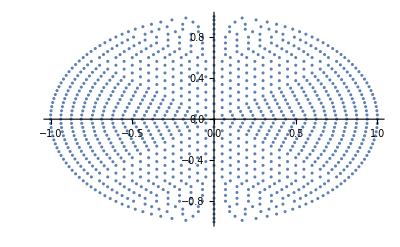

```mathematica
ListPlot[%11]
```

```mathematica
ListPlot[total_grid]
```

Rule::rhs: Pattern total_grid appears on the right-hand side of rule System`ProtoPlotDump`modelData[WrappedValues,total_grid,Charting`Private`Tag$5321]→total_grid.

ListPlot::lpn: total_grid is not a list of numbers or pairs of numbers.

ListPlot[total_grid]